# Homework 2: Modeling RT

First, you are going to try to fit a so-called “half-normal” distribution to the data. 
That distribution has only one parameter, which is its standard deviation σ. 
Play with this distribution in Mathematica with the Manipulate command to see how it varies with different values of σ. 
The mean (expectation) of a Half Normal distribution is 1/σ.

```mathematica
Manipulate[Plot[PDF[NormalDistribution[1/s,s],x],{x,-1,15},PlotRange->All],{{s,1},0.01,2}]
```

```mathematica
(* min std and still plausible mean ~10 s *)
stdMin = 0.1
(* max std and still positive *)
stdMax = 0.55
(* remember that mean is the inverse of std dev*)
meanMax = 1/stdMin
meanMin = 1/stdMax
```

0.1

0.55

10.

1.81818

Create a prior distribution for σ such that only positive values have nonzero probability (because standard deviations are always positive),  and such that the values of 1/σ have a relatively wide range. Also, make sure that for values of 1/σ that are much larger than what you suspect is a plausible mean response time, the probability will quickly get very low; remember, it’s the mean response time we are talking about here.

0.3

3.33333

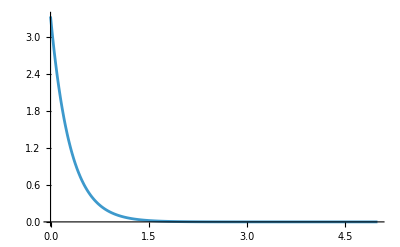

```mathematica
(* assuming that the prior std ~ Exp(1/about.3) *)
meanOfStdDev = .3
lambdaOfStdDev = 1/meanOfStdDev
priorStdDev = ExponentialDistribution[lambdaOfStdDev];
Plot[PDF[priorStdDev,x],{x,0,5},PlotRange->All]
```

Prior predictive

```mathematica
Nsim = 10000; (* the size of the sample *)
generatedRTData = Table[RandomReal[RandomReal[NormalDistribution[1/RandomReal[ExponentialDistribution[lambdaOfStdDev]],RandomReal[ExponentialDistribution[lambdaOfStdDev]]]]],{Nsim}];
generatedRTData
```

{15.6267,0.253526,1.4161,1.70028,2.58043,1138.4,3.53809,6.51391,1.99954,13.624,10.9147,0.923031,1.12063,17.7001,7.80955,0.487619,2.22954,3.50311,19.0657,71.3549,0.581503,14.138,1.68278,2.25724,0.521375,3.32007,0.476657,28.0847,1.32288,19.4854,-0.217601,1.70341,3.53962,1.13865,6.97714,5.26658,1.35981,0.0598755,0.591121,2.53847,12.5575,2.42107,4.71344,4.80574,0.00446466,1.02138,1.25764,0.233908,4.90174,1.02145,4.63017,28.964,1.51759,24.3832,12.5999,1.03918,1.08896,0.865753,0.252092,49.4219,1.81275,1.42154,34.4152,7.02938,3.28998,1.50165,15.3107,59.941,2.82776,3.75391,0.695345,0.737356,0.529706,0.553417,22.4168,3.18879,7.88101,1.35303,3.13791,2.10041,0.322759,0.600581,10.1655,1.8749,2.66303,2.23264,1.89236,15.5295,3.24887,41.5056,19.521,3.78102,1.17321,3.52945,2.30587,14.8327,0.37186,0.758885,19.9248,0.818328,0.337397,0.813134,410.709,0.247064,1.64006,1.37183,11.469,3.19492,0.426757,14.9057,15.5331,1.83175,2.75741,4.47405,1.55431,10.5193,0.157025,1.61564,2.48655,1.63528,10.8008,18.1023,1.12171,0.116936,1.26183,1.54031,1.66668,2.74435,7.37674,6.95791,68.9529,5.24662,1.5945,0.801876,1.67827,1.91792,0.549006,0.891073,2.73533,-0.00625633,2.24975,3.37087,4.13137,1.64716,1.195,13.8039,0.685013,3.63832,4.27192,2.56797,0.936887,1.45659,1.75557,29.9628,0.156179,0.445792,0.0965808,0.322115,0.712383,5.49339,2.61018,71.3329,0.975406,1.11248,2.16278,8.1094,1.82987,4.97477,0.777347,0.13331,0.20786,1.80378,3.25717,4.69911,1.32155,0.227847,2.33927,12.2064,0.930608,0.796924,2.16287,1.38369,0.800703,2.06802,0.474511,0.0890613,4.36558,2.78409,2.60606,3.95341,0.442852,2.09711,0.111151,2.01846,1.4367,3.29995,0.0447998,0.600643,1.86887,12.0736,3.31464,0.534378,1.86481,0.570542,1.56971,1.77168,1.79819,28.7244,1.90603,91.41,3.62408,2.721,1.0395,1.84199,1.10927,14.244,136.741,2.34268,1.44655,0.189891,65.9163,1.15665,200.817,3.62442,1.11518,3.71068,1.04269,0.941492,2.07545,7.10718,33.6,0.594229,2.60782,0.160921,0.176412,23.5608,1.25597,3.81353,0.72362,23.3195,0.470317,1.95276,6.09273,1.69371,0.507005,5.07201,1.16833,0.387402,0.244341,1.89945,2.20034,6.90057,8.07645,2.59777,108.232,3.31582,1.24565,26.3234,1.63277,0.28844,20.0583,1.00519,5.10261,1.94054,35.4885,0.854099,4.88505,5.83729,3.46496,2.47576,3.43849,6.53156,69.8795,2.38555,1.45379,0.650898,0.142944,0.556267,6.59094,1.81485,15.093,1.24373,1.7377,5.08724,11.9861,11.1573,0.103664,1.69532,0.967607,6.87743,48.9682,1.67706,12.5737,0.86205,0.606799,0.516538,7.98959,1.43732,0.714293,1.19036,0.94744,10.6408,2.21862,5.1846,2.86643,2.63374,3.91879,0.244645,4.471,1.28317,19.2649,2.85765,2.24668,0.381516,10.4389,1.91493,0.511434,0.0371062,3.03561,5.66743,1.05965,1.38736,3.57734,0.000762137,0.525658,2.29819,0.77119,5.24867,9.27589,0.00578573,1.90085,0.057143,1.90013,1.22066,2.20431,42.8781,0.231855,103.451,2.66522,0.212607,28.9323,5.16009,0.472732,27.8433,0.538678,0.132089,4.94577,0.699214,0.52541,334.116,3.10069,0.184186,5.58964,0.334772,13.2776,2.54421,12.883,5.55497,3.24362,0.737185,0.839689,15.5322,0.681363,26.9313,2.08356,1.43283,1.98004,0.987654,4.92239,2.93225,2.10558,11.768,2.86454,2.10412,3.80504,1.08115,0.569516,8.88594,7.1062,4.72808,0.48596,2.04165,1.25442,0.000503882,3.6125,3.64523,0.162399,1.69205,0.646261,0.155854,1.57968,0.0591965,4.35588,1.40802,6.69854,3.51939,8.75902,1.64236,0.206094,4.88985,6.17239,5.13599,2.23121,2.32372,21.2761,1.607,2.6516,0.012762,1.43227,0.208639,1.6928,0.722679,0.440232,2.14673,3.87385,4.66522,1.47397,46.0268,2.16117,1.89589,0.085063,2.37161,1.86802,1.35783,4.12918,0.657177,2.11319,1.84495,2.28434,0.435272,10.2013,0.811936,0.574928,1.34056,0.977296,1.69135,101.693,1.46312,1.64716,4.22205,1.15348,1.54768,0.62018,0.401955,2.62244,0.952398,1.00168,1.71764,2.05786,240.086,6.10103,9.14436,14.4834,0.638143,0.542787,4.21308,1.87579,3.34085,5.27346,1.50148,0.424361,1.81222,0.134502,1.93263,0.0103994,0.481758,1.71052,9.09956,0.446901,3.2639,0.474799,1.91773,1.21357,49.2332,2.90518,1.27206,1.11624,46.0248,2.57614,2.84896,2.43241,1.92554,9.0785,4.22596,6.40547,0.571891,37.7108,8.54335,-0.229111,1.26205,1.76828,3.29688,0.599855,2.84977,1.05772,2.2098,2.77646,8.99237,0.129797,0.52605,131.749,4.36638,36.6397,6.20043,2.39572,12.2938,9.24553,1.98444,7.0553,1.29309,1.76193,0.225225,0.381787,9.94922,1.04446,1.9983,0.201612,0.537785,9.39016,15.8972,3.90061,8.96606,0.183483,5.62221,4.43224,12.2483,6.17408,0.217122,2.30269,7.54793,0.567323,219.501,1.04653,2.29811,3.57353,0.493773,1.3641,1.86055,29.7011,4.77726,0.0920217,0.133136,1.2835,4.37887,1.69626,19.7317,1.20818,1.29469,2.15658,9.4414,4.83237,5.88888,1.66356,1.19404,4.85065,4.41987,3.32195,13.4406,0.627583,0.679699,14.0279,7.96451,0.450693,0.505143,1.01763,2.4843,52.4405,2.36074,1.67324,2.0419,1.29826,9.93591,0.942134,0.121222,0.0728842,1.68345,20.6373,0.207851,0.10605,0.713687,0.729669,0.330648,1.22959,0.500581,28.3677,1.58394,0.832241,0.899256,1.07668,39.9036,1.19483,15.0059,5.267,1.00258,0.778503,0.0262808,52.1568,2.28548,3.68697,0.222029,10.7835,11.8763,0.258426,4.68396,4.5153,4.76203,2.33402,0.0983935,3.24126,0.916375,1.23596,1.2523,2.0754,3.03252,2.40132,0.0140103,0.288072,5.84298,1.74531,2.33649,0.402106,2.4376,62.0617,1.16244,8.36278,0.209509,204.176,21.6073,3.24463,1.00163,0.444288,0.0324613,46.5715,0.847956,7.77406,25.3942,18.7231,0.565244,0.829191,2.92133,0.773546,0.294068,1.46449,0.31249,14.0399,0.404723,3.07769,3.70322,0.527321,0.933693,3.70668,27.0097,2.87352,1.86134,1.30554,0.670677,21.3163,1.62788,7.01042,2.54156,5.52574,0.0393163,3.20534,6.49021,7.24094,2.87535,0.26441,0.90697,0.214321,1.68713,2.16272,8.86052,1.34971,17.8,0.926727,0.674167,0.382764,3.65107,0.3044,8.32639,0.0330163,0.228627,13.2735,0.0321715,25.797,0.591499,2.59502,0.635041,9.27311,2.69419,0.358056,0.537572,2.93342,2.98598,1.49093,5.47221,0.0963488,8.5148,0.151253,0.600239,1.68371,1.94167,1.29903,7.06681,3.84242,2.42731,0.855321,12.79,0.0916849,1.48537,14.3288,2.8778,1.81315,13.5207,6.87537,1.38498,0.497255,8.41742,0.231012,1.7983,1.73967,1.37914,3.32838,14.7699,0.175145,2.64096,1.24005,0.286488,4.7635,10.3338,2.57481,1.27193,0.7853,127.756,1.25742,0.156924,2.06137,12.5099,82.2337,1.56561,0.375816,3.1647,0.169284,0.748858,2.08881,0.103803,1.457,4.01625,10.5056,1.46326,1.35342,2.25031,214.889,7.50314,0.98979,1.21882,55.2191,143.276,0.282842,4.91242,1.14267,1.4127,1.26222,0.0125538,2.62734,2.84158,2.40338,0.279327,14.6399,16.6365,2.81308,6.64863,5.5117,4.33006,0.453773,0.471722,-0.0769918,3.131,0.836119,1.57166,1.05874,0.260588,1.55899,76.9113,2.79893,0.744217,0.410225,0.24453,3.98412,1.64195,8.26097,4.28133,0.919604,0.955491,0.536085,4.27201,2.37615,0.743704,35.106,0.151017,0.469643,0.0617553,0.724663,1.29644,2.65956,1.16429,0.00108588,1.0802,10.472,1.11905,5.01076,0.396367,15.2808,1.83234,1.05974,1.12015,19.5145,0.448218,5.3505,1.52672,1.1843,20.0822,1.44736,4.75731,0.421692,2.49016,2.86613,1.22168,11.2321,43.2979,1.19979,1.61266,0.957467,9.9315,0.655015,0.158793,1.21521,0.808276,7.47127,0.79892,0.213793,1.52726,2.97968,3.21143,0.862526,2.51734,0.419827,17.2365,4.18036,6.16396,24.9411,128.03,2.53643,0.750113,4.55277,3.84081,11.801,8.75429,0.163235,4.80104,12.5973,1.64228,0.130833,173.26,3.20502,5.38202,3.5729,3.42622,27.0651,0.432016,0.312233,1.03759,8.84077,1.53446,1.38133,15.0289,12.9457,2.89971,1.49749,0.645228,6.83338,15.8762,7.80617,33.3183,0.870833,0.924559,0.339107,3.22965,3.20792,0.871928,110.967,7.10399,0.611391,2.0866,1.46312,5.98302,0.5918,0.237574,2.12799,2.83022,3.68311,8.3066,8.07189,3.13609,0.765726,0.460652,0.101652,0.780728,2.73185,2.10685,5.86018,16.9386,1.8315,0.37224,0.321856,0.246102,0.784599,0.823945,29.0585,0.978297,2.39353,5.26014,0.436989,1.32578,3.16376,0.165638,3.11346,116.028,10.9323,0.0503166,0.0173812,7.88197,0.869116,13.0402,0.450083,0.391619,1.19228,2.80797,0.225517,8.53043,1.97671,0.853845,1.03207,2.00394,15.837,4.50381,147.598,0.0712097,1.10225,4.0112,19.2853,0.223573,0.681346,1.42526,33.077,18.9012,0.290538,7.83519,0.867133,2.06142,4.46227,0.796076,1.11372,3.77857,3.54283,1.66382,3.46692,19.7381,0.104527,1.26071,1.39979,28.6507,0.565386,45.6323,38.4411,2.27659,2.3705,1.93157,7.30338,1.52282,10.3555,1.90917,10.9971,2.85195,1.12443,19.1173,0.943275,2.01954,5.17371,1.26095,0.403483,0.513266,6.82981,2.64021,1.48412,0.389811,1.35352,1.02778,3.57125,0.512098,0.217527,4.22,35.5326,14.5213,2.1532,0.524781,0.192278,0.431488,4.08926,5.87954,0.369055,0.109707,4.18723,4.07053,53.5818,1.4168,0.807556,2.49068,2.96508,1.54943,2.02007,17.4932,0.242398,0.38084,3.59045,1.11575,29.6876,1.30827,0.996233,2.23707,0.20932,0.473293,3.45138,1.54971,2.62958,8.55069,0.579428,0.998753,17.7451,0.20949,0.433145,11.9255,0.409918,0.796165,3.9624,0.971222,0.460506,0.526045,1.70438,1.2457,5.31442,2.58582,0.242589,0.37311,7.76597,2.76921,2.87086,3.4513,0.511537,20.0526,12.825,12.7984,2.46869,0.0418895,21.71,3.74097,7.76743,4.40166,0.138533,9.33912,0.190344,15.6588,1.64832,0.254008,1.57073,3.98137,0.0329632,1.18275,1.33264,1.20089,3.33593,3.50016,2.09381,14.8036,3.96704,0.0124999,19.2394,5.15487,-0.223598,12.0635,0.124563,1.59236,2.82583,7.89436,0.631809,1.02201,1.29538,0.155619,0.554104,0.488429,4.36858,7.1612,6.08372,1.23944,185.01,2.64297,1.73663,0.694984,0.675391,0.626447,0.387918,13.4034,1.27409,0.584489,1.91723,1.00634,0.175636,10.6283,0.836147,14.3905,10.4308,0.58271,2.9536,5.45889,3.09562,0.690021,1.68731,0.598633,0.55221,6.86098,3.64863,0.540819,11.4416,6.85967,0.224897,1.14736,1.12618,17.6181,2.48776,8.68973,18.249,10.3439,2.73296,2.71007,0.100877,1.94654,3.7428,0.316521,2.21631,0.0572755,0.396517,0.97957,2.07494,0.84561,0.53564,2.60749,3.28342,0.958698,0.605379,1.03563,0.719613,7.05406,6.38494,1.50751,0.99192,8.9124,2.49029,6.0188,1.57789,0.493783,1.97467,3.62815,0.153273,1.1221,0.241187,2.68949,2.80072,8.92941,1.40406,113.455,0.692839,24.066,3.60146,0.306807,1.21566,0.00786683,0.560577,0.721582,29.5662,1.48328,1.32284,1.5868,1.68134,0.159301,2.14074,0.202803,3.11215,2.17748,1.89705,2.40609,0.520716,17.9489,7.96529,16.1902,0.255365,1.21041,0.548464,5.327,0.979663,6.06246,37.7528,0.82408,0.760853,1.22654,1.45025,7.06235,21.0861,13.4732,0.897621,0.363901,1.30225,1.90698,0.102743,1.09769,0.517444,0.496547,20.8021,6.41183,6.38647,10.6113,0.618366,1.25773,20.9751,0.98805,1.22628,1.36722,0.309217,12.5147,1.27422,0.398871,1.65817,1.34917,10.637,1.52651,22.3498,0.172321,2.93515,5.98183,0.142468,13.6479,0.732896,0.839043,3.9265,11.2127,1.86191,0.477545,0.181177,0.872086,2.75976,5.10543,4.83317,2.50038,0.78847,4.44262,16.8313,9.60994,2.9646,10.7369,1.17465,0.275852,0.214352,2.49563,0.0578036,1.45482,0.908683,2.40109,0.150732,4.00087,3.54239,25.8358,0.59293,10.5555,0.71847,0.46135,0.676456,0.619985,855.544,0.400801,0.826407,1.5876,2.25183,0.638266,3.59758,5.81184,0.329312,3449.61,7.54591,0.674381,0.702715,2.04118,0.915312,1279.98,18.1508,14.4752,2.92889,0.757651,2.61262,5.30574,3.25643,1.93047,0.536239,10.4737,10.8732,6.00967,0.0232194,0.991352,0.9226,3.05907,1.76328,-0.0245179,18.051,0.23724,3.3821,1.60676,1.23963,3.8658,1.81594,88.2135,0.757456,2.49255,45.319,1.15434,6.09589,0.706057,3.08556,1.39979,1.58349,0.441062,0.912143,0.606984,3.71475,3.51452,2.89114,23.0536,1.63982,113.806,0.524365,1.56047,0.285247,0.539531,1.3209,0.0782785,2.90608,11.8866,7.27111,4.3858,5.62823,0.191021,127.501,4.18214,7.6366,0.120112,0.27951,1.87918,3.15032,0.784757,35.4175,1.89821,1.80693,6.45431,3.02888,0.710411,1.21133,3.27579,2.0058,22.1641,1.3316,3.62533,3.00236,2.56787,24.1236,0.362713,5.7564,5.90425,4.11383,23.3432,19.7314,2.36924,6.88634,19.8304,0.10011,3.13751,0.947052,5.12472,6.37185,22.7799,10.9272,1.42816,6.8134,5.02223,2.7642,54.052,6.58331,1.91521,2.81964,5.5647,1.24785,2.52326,2.45574,2.48264,93.6692,9.57329,1.29355,0.550899,77.1507,1.84556,10.5157,0.367304,44.0038,5.32619,0.0671055,0.688817,1.23873,70.1307,5.84832,2.59087,2.50329,0.492369,13.351,3.44719,4.28754,2.90308,1.51351,15.261,2.16736,1.17887,2.00766,0.445701,0.655465,1.96191,4.51913,16.0754,8.31897,10.85,2.41499,2.33791,0.0208504,3.31692,5.04026,1.75959,1.38937,0.212312,2.60088,2.54081,17.1483,10.583,0.105245,0.649968,1.41108,1.71043,3.03324,5.44945,1.27978,1.41676,3.60136,3.54965,7.17691,2.86667,7.31306,0.15398,1.34298,1.15024,4.16571,4.55191,1.12921,6.92494,3.46313,0.782901,2.3455,0.543905,5.17401,5.84881,7.55429,2.85262,2.76734,0.970156,0.482201,28.1581,54.1623,1.2021,2.75548,6.29383,10.5532,0.00236868,1.97864,5.27158,2.30306,52.5427,9.57656,1.34766,0.378669,0.468515,1.1324,1.18489,0.267308,1.8081,0.446642,0.741835,2.81969,0.57157,4.92408,5.96414,0.655173,0.523555,0.686441,1.44651,1.11407,18.4307,0.607068,3.16393,0.299269,7.71187,0.679442,4.97692,1.33463,0.278629,0.677901,10.1345,17.199,8.93848,1.30266,3.64665,1.36055,0.599391,1.21257,5.56836,8.07249,4.54664,1.47437,8.48681,87.9027,2.80191,1.09751,0.389943,2.01224,0.338905,0.59059,1.16936,4.52726,343.186,5.67935,3.2883,21.71,762.176,0.846383,1.87615,2.12821,7.31546,35.772,0.794436,0.285471,0.197308,2.9045,0.372956,2.45802,3.09086,0.57722,7.40476,14.085,6.05756,8.11439,8.35955,1.09971,0.972969,0.361261,0.398832,1.47122,1.00759,1.11708,10.7983,5.36029,4.43343,1.2978,6.98394,3.99851,0.11611,3.16719,8.79993,1.16006,0.539364,23.7222,1.94278,1.66358,1.15527,1.45035,0.981214,8.82644,1.33698,9.32264,2.65276,0.951374,1.61944,0.943458,0.285325,1.84643,1.46948,7.00454,1.98935,11.4009,1.77531,0.702322,0.12417,4.60011,14.8278,66.3392,2.25809,2.66821,0.152395,0.559719,3.98388,0.230552,6.43439,0.090126,1.2121,1.72888,1.52591,7.73908,14.1863,0.571032,6.84116,16.8828,5.85283,1.08132,2.91101,1.87439,18.8759,1.33405,3.29571,1.04353,2.94488,0.916049,16.0983,0.471033,2.6739,-0.00147458,62.0119,0.0490579,0.0796185,0.420928,2.5514,3.34658,7.6113,2.82849,1.39131,9.51978,0.485944,7.22973,3.12694,1.34288,0.0959094,0.959694,6.05948,8.07078,2.56565,4.53754,0.266841,17.2346,22.5812,2.82553,5.36149,3.18138,0.0787361,7.12673,6.19264,1.63515,7.04094,10.0674,0.536257,1.81466,0.532842,5.55293,1.38643,1.46585,8.11899,147.598,3.25437,2.14679,3.1612,1.26014,70.5894,6.53302,0.546156,0.562558,83.3953,1.62759,0.499427,0.338933,2.40802,2.22676,24.6468,11.0903,1.59944,3.76556,36.2482,3.24537,7.2161,50.1539,0.967309,1.1486,3.84509,1.1053,1.50322,3.58679,0.0737742,2.40886,6.90356,8.98319,0.997876,3.44314,3.31101,212.13,0.348291,1.89303,1.53892,13.1537,3.63617,3.49714,5.2609,4.9386,9.65375,1.09222,16.0211,0.793701,3.78727,1.64021,2.88704,22.4923,2.68928,2.70336,1.47998,0.591436,17.2718,0.192327,0.985554,1.78129,0.00394342,1.75601,1.6759,3.67838,0.581404,1.76765,0.592624,0.493867,0.561457,0.399308,1.86834,5.69239,3.00788,0.175151,46.5501,2.37098,1.53649,0.319135,23.5368,3.8533,3.75852,47.9694,0.00870305,2.94948,9.2696,0.804784,3.82608,1.18255,35.102,5.47131,0.0844808,1.20341,0.365267,20.1781,2.02078,9.17178,0.209046,0.215005,1.29182,17.0429,114.108,24.478,1.75233,2.19013,0.0249682,5.94397,6.28333,20.0658,1.56219,0.598848,0.0852174,1.64336,4.8762,0.227631,6.24521,0.210722,1.8011,1.60299,2.06889,5.72076,3.4545,9.42649,1.54064,5.23803,0.361725,1.42946,0.91278,0.327381,6.1767,0.108378,2.17002,2.4483,22.1833,2.15989,0.534516,1.08616,2.31444,1.33738,0.828693,0.127513,6.63937,16.3314,0.342547,2.09182,1.25158,2.55128,17.9568,6.33028,12.4986,0.75342,0.548442,0.799399,6.62848,0.228775,2.30014,15.8577,96.5689,1.12522,0.383203,1.24951,0.498793,3.19296,2.22664,1.10709,5.03629,3.97182,4.68702,0.320958,0.158544,1.29856,1.34195,5.38273,3.80476,26.5723,2.02446,2.89143,2.57746,3.31404,2.14356,18.5233,6.6343,98.5802,10.4649,0.87558,15.5882,71.7543,0.307573,1.62112,3.56545,0.551373,3.35085,0.0679131,3.69538,2.53759,27.8271,1.49624,0.284755,0.0263138,3.49612,36.4893,1.1292,2.13352,3.41416,3.50196,0.485554,0.0658148,2.23603,4.63189,1.65514,10.0831,0.0444804,0.555393,3.24116,20.4036,4.14877,0.102384,1.60547,8.23364,9.84379,0.107665,0.419869,0.832567,0.480246,1.58456,0.0472403,0.651025,0.153924,6.23814,6.65873,2.0781,2.54923,1.20761,0.640037,2.72238,2.601,51.1007,1.81063,5.67655,6.25761,20.8238,0.432357,0.250752,0.601214,80.9811,2.32304,1.95935,5.45691,2.43047,1.28347,0.334175,0.0678649,1.81864,0.867626,13.2046,3.30636,0.973957,4.40287,1.40457,0.865149,2.03921,2.06579,0.974329,2.43948,0.880387,0.356633,5.10362,0.227976,1.37332,0.946096,19.4751,4.52053,0.120965,8.99755,9.23591,1.98323,0.0642435,162.543,1.51175,4.05926,11.275,85.0551,22.9304,7.68074,8.61266,0.136427,0.781013,7.13229,2.30537,0.885142,1.21627,252.641,1.58836,6.02104,0.679705,16.5897,21.0009,2.52043,0.403533,2.85543,6.77266,14.0848,0.21831,0.0900942,3.12002,8.34903,4.04603,1.82182,1.11996,8.6607,0.823372,0.883175,12.7652,10.8319,7.79446,3.75054,0.484691,276.221,7.3248,9.02462,0.928569,1.93605,0.273737,86.1982,3.62869,4.94411,1.4214,0.205262,1.24103,56.217,0.0850022,0.865188,0.655878,2.35175,1.70711,74.6421,2.6214,2.71791,60.4445,0.583377,7.70494,0.601963,0.293699,0.42467,0.920994,0.263767,0.865656,0.644104,1.16654,1.22268,2.02724,0.32709,0.644655,5.79139,0.839023,13.9381,7.66041,2.19321,5.85992,0.264291,5.30074,0.886519,0.666704,2.85603,5.758,1.56771,26.8819,21.9898,1.88388,7.5182,0.904238,11.1374,25.6028,13.4422,2.7093,2.89784,0.5626,3.71495,13.4195,110.584,71.5705,0.37703,0.567346,0.844894,1.4935,6.3521,3.16183,4.16673,1.24107,5.39547,1.0263,0.892357,5.10407,1.47287,1.9529,1.37833,5.57125,0.719164,34.1391,1.71241,1.16682,6.41633,0.778446,0.901235,1.41375,2.05647,14.3845,6.25078,0.973756,2.77879,4.16214,25.8118,0.567155,0.951384,2.56777,2.62648,14.0928,2036.08,0.108371,10.5803,1.10488,7.91088,0.689355,0.236238,62.2805,0.932115,6.64107,2.30233,0.898107,0.973188,18.3672,1.04694,2.42209,4.42693,3.02651,0.757995,2.19568,2.17103,5.6307,8.25053,0.847441,108.217,0.982452,0.553016,0.87537,2.18607,26.8373,16.4241,0.492088,0.828582,4.0974,2.48741,0.789675,3.4211,27.9102,0.232775,1.32525,97.1383,2.36858,2.02637,3.47965,13.871,1.43387,0.3216,0.832641,10.5186,15.3782,1.4175,27.9336,2.53878,6.00417,5.45983,4.74362,9.79619,31.2587,2.78776,3.26928,1.40423,3.09361,0.23793,0.903748,10.1447,0.875398,3.48311,0.702856,7.6008,13.1292,30.6862,2.15846,13.3836,0.216235,1.97636,22.0102,3.98488,5.1978,3.16631,5.7997,0.714434,186.291,1.29084,0.865907,23.8653,1.15762,0.183955,6.3679,12.2894,1.85365,1.6847,3.40327,8.84155,259.167,2.53357,1.49765,4.44543,4.59165,8.65453,0.233559,0.523934,0.0777816,0.772255,8.70385,6.91825,0.113309,1.77436,12.9777,1.21314,2.88058,1.71631,3.76548,1.22922,39.0832,1.42294,19.1137,6.33127,0.00310373,10.8269,2.39027,1.37359,1.08291,18.9076,0.192387,0.299246,0.461832,1.47284,3.68977,0.661193,3.13196,5.48282,1.9783,0.292945,0.396922,1.45257,0.0352721,3.16197,23.6279,7.60268,0.493478,10.3525,2.46626,5.08969,35.9683,0.228211,0.613233,0.225852,0.158248,1.16913,13.2758,3.88153,4.67666,3.5183,0.029773,6.32503,15.0533,3.228,0.900005,23.739,0.919135,0.0329238,5.06787,0.0879459,2.36456,27.0364,0.913744,179.587,0.863202,14.6231,2.79643,0.459931,1.03709,8.2082,2.2112,1.5059,1.39834,0.851807,8.45245,0.268597,0.73851,1.65726,1.68721,187.059,63.0381,1.20746,5.71922,1.18831,0.386984,5.60512,1.17577,2.00743,0.457139,1.22245,1.21619,26.3624,0.208945,0.769333,7.29642,1.82774,2.89128,1.54297,1.84699,0.009903,18.0795,2.98832,4.56635,2.23709,2.32613,0.751276,5.56795,9.77571,129.659,4.36032,4.03901,0.461369,14.502,0.0803928,1.10163,1.21629,2.18768,9.37986,17.5374,0.402217,2.16149,2.03295,0.98036,0.232965,0.0724411,8.26377,0.75275,2.70426,0.32879,3.89861,4.17678,0.876415,0.224087,6.62034,8.66408,0.29032,0.512349,2.49817,6.7712,4.16653,0.774363,5.45754,2.63058,0.787995,0.720696,18.5249,1.63146,1.01306,2.12743,26.9543,2.37002,1.07997,0.620631,3.377,0.556087,0.933579,6.71763,0.225093,0.286876,4.11559,4.4733,20.4692,2.64938,4.22778,0.609702,5.99369,0.515183,0.129707,1.25178,0.546369,1.0555,9.2055,1.1194,55.4387,1.29742,0.512063,2.4488,1.05179,0.827558,0.0288779,2.98128,2.16414,2.00847,79.8426,6.68022,0.116159,3.3224,1.33607,0.639896,0.56093,0.227361,5.90353,0.45583,17.427,14.2121,1.009,0.799175,0.369478,1.05717,0.507145,0.427066,1.3567,1.3013,0.588246,0.256928,4.24578,4.10958,6.91797,0.30123,3.863,0.0701223,3.4325,0.394642,0.661877,7.57672,2.08288,1.73319,2.65775,1.8248,7.39386,6.1288,3.31183,4.13736,5.03604,2.5638,1.08759,10.1395,1.57231,0.731998,11.2661,16.7577,5.76681,5.94549,0.0689966,0.135866,0.372717,0.596275,0.503045,1.8716,7.8349,6.18683,2.07522,3.23681,1.42066,1.85803,0.0519019,1.03448,6.00529,9.02124,3.64183,0.649459,27.8569,0.681777,0.802039,1.34222,8.6384,3.23889,0.879174,0.141069,1.35353,0.951486,0.955027,1.00571,13.2773,3.09334,11.276,2.56597,1.69751,0.99679,10.2866,4.37971,1.52531,0.14327,1.93959,0.991178,5.26153,1.12826,1.42541,0.457432,10.1846,0.361741,1.33317,0.185264,0.171626,2.54594,2.86928,4.0691,1.16688,2.20088,0.838135,4.53339,0.101158,1.28836,1.49274,3.64452,0.643998,19.2945,2.91934,0.725934,0.920465,0.864906,0.178372,1.13293,7.16402,13.546,3.35514,7.47889,1.26338,0.59711,0.0664897,3.28432,2.4659,0.810281,7.39654,5.94074,3.26293,4.54606,4.88052,2.5446,6.22673,1.4097,0.133976,4.04342,4.01133,13.3629,3.13084,2.00263,1.72882,3.04555,1.19363,1.05578,1.5636,2.25807,3.00348,6.78897,5.81253,1.55375,1.58655,1.61644,0.564268,2.41213,9.12031,0.339399,1.0109,1.227,27.596,0.388551,4.3317,1.06196,3.61625,6.74243,1.45033,0.263084,15.8134,0.185363,0.234381,0.696669,1.93346,3.52162,2.32525,35.6295,4.6451,2.08392,3.41608,0.893774,4.15707,1.96688,1.05166,0.431745,0.325349,3.53981,2.32512,7.67748,0.787551,73.9037,1.80233,0.502895,9.64264,1.8652,4.24653,53.8922,10.106,1.01017,0.851487,1.35956,5.30417,1.67762,0.448957,9.36624,0.691009,11.6297,4.87727,3.17256,0.0841734,0.435373,1.20068,0.157339,2.96539,1.84762,1.15855,2.80177,3.29785,7.58528,4.06745,3.10061,0.479337,2.52165,10.936,2.49002,427.422,0.341711,14.1297,1.26794,1.5936,4.00624,0.509312,1.90529,6.96603,6.30093,7.30762,75.7314,9.97289,1.40842,2.71381,2.70477,0.701938,1.54473,1.97739,4.55551,0.70472,1.24979,2.98024,1.25089,4.82191,14.1223,1.20936,0.590378,2.37624,2.31361,7.33994,12.3277,5.43069,1.40403,0.771818,6.11794,0.663886,2.03343,0.404064,39.9774,3.38957,77.3009,130.037,3.18104,0.19251,3003.1,24.1339,26.7719,0.0278048,0.305291,1.29658,4.31302,903.745,0.508838,1.41285,1.51116,0.918891,2.12593,2.53401,3.84587,1.47026,4.30864,94.2606,2.80245,5.01469,0.0308201,0.625767,0.924056,1.08113,1.62862,3.2668,0.767675,2.0407,11.4889,2.81341,4.71981,0.656175,0.497419,5.49681,1.28899,2.08063,26.5125,6.88586,2.05778,0.582834,2.49093,4.55097,5.8045,1.49601,0.854344,0.338986,1.91516,1.54669,6.44171,1.06634,3.13087,0.26781,3.94636,1.2717,11.3711,0.655709,6.31452,2.82235,5.80398,10.4701,15.2752,1.24613,1.20794,106.548,20.7144,6.37858,1.82207,1.42365,0.464329,11.6047,15.6265,0.663307,4.52383,1.01706,3.47497,0.978706,0.384931,2.2466,6.61653,0.8165,2.13816,0.621428,2.04733,0.761428,1.83374,1.30033,0.00899742,1.49494,7.63942,3.45966,4.92308,1.42776,1.13219,3.84881,0.317549,0.455889,0.480648,0.765873,2.60787,0.588829,2.51847,6.70176,12.1578,0.0424024,0.951129,0.997479,4.70286,0.846648,5.34348,1.01026,0.165426,0.0971822,41.1281,0.936593,8.26214,1.26944,0.662633,0.977914,0.237732,0.593928,1.63724,8.40543,2.57677,2.05914,3.94351,1.72985,0.200764,13.5879,48.0348,2.10544,5.09743,24.1816,29.3558,0.185175,1.56342,3.09013,0.480503,44.9365,0.825979,2.86967,0.221297,3.07567,1.29058,0.801166,4.38013,2.73056,6.46784,0.287762,1.89503,1.85514,3.102,11.2178,0.0859889,12.6414,1.36418,1.91937,0.754658,2.32085,0.728615,2.48317,0.746744,4.0119,6.59507,8.07767,28.2068,5.58197,20.5163,14.01,0.542606,0.666017,0.547699,5.04169,0.844606,13.4556,2.53233,0.979508,1.83991,5.64284,20.4521,2.19566,0.0724218,1.27923,3.06584,4.89068,2.95865,2.43101,0.462522,4.75395,3.40065,0.718494,2.34836,32.3919,4.21209,0.236783,50.7248,7.17769,0.940307,14.2756,3.35448,0.857566,10.4948,3.77521,1.69451,0.0547137,16.9741,0.725797,5.001,5.84097,5.73078,1.10263,4.25467,1.51938,43.9811,1.78127,40.5611,27.0627,0.787375,1.72,1.04409,0.74269,4.06291,0.311757,0.325799,2.90085,9.49959,0.608847,0.463648,2.70103,3.58587,1.76119,7.45635,0.0978138,10.2416,6.9392,0.222112,0.855474,0.399048,0.322226,2.6714,0.817895,4.36963,21.8335,3.1689,3.86679,0.388182,2.11534,0.105081,0.456905,3.59824,2.43062,0.337658,10.0665,5.13511,1.26361,1.0396,18.5574,1.46382,1.32812,4.50395,5.24041,3.60978,0.214302,3.33984,3.20667,0.756959,7.96159,1.09537,0.188795,0.819753,1.70361,1.97487,1.08121,43.272,3.80715,0.458518,0.696483,19.9668,0.64318,1.05346,5.98056,7.59264,0.304967,28.2587,1.398,1.30026,3.94169,2.23967,2.35903,1.00017,0.741655,8.86296,1.61441,2627.3,2.94512,0.835384,8.41778,5.00915,1.85859,0.346214,75.1094,1.32043,4.04674,2.07733,14.6674,1.27078,1.81643,0.380696,4.95654,0.77196,18.043,0.977723,0.744203,0.570316,1.53446,37.8633,1.10094,141.948,2.01098,11.1423,1.77888,2.06421,2.08361,0.00529441,2.03542,6.44641,28.5449,1.04549,0.45012,15.0896,1.61472,4.32635,2.86951,0.487574,4.14279,1.28205,0.330966,53.0791,2.93581,0.0119457,3.20798,4.71827,9.26961,0.608051,3.65106,3.31929,0.151046,5.14045,18.7548,0.64685,0.283953,0.239756,210.182,0.159667,1.36992,2.4165,2.62949,82.4352,0.724,2.3258,235.198,3.50663,2.31296,12.6366,1.43969,-0.277745,4.21981,7.57594,8.73924,2.19639,0.438008,8.81147,3.66836,2.32727,2.25642,0.149618,3.27022,10.4106,0.855379,4.1299,0.37081,3.18009,6.35303,2.71534,1.06053,10.4993,3.98158,0.816136,1.83996,14.1457,21.4859,29.7659,1.60562,8.42309,1.70979,2.18152,5.13952,0.948074,1.18808,18.2419,2.95126,2.81305,1.06987,7.31577,3.36647,0.830516,3.27459,7.42064,8.55308,0.279059,1.85717,0.971903,2.88058,0.581553,0.901341,23.9945,2.31906,1.07224,140.09,0.0666117,4.32912,33.8082,20.6283,1.49097,1.44669,4.8609,1.54781,0.491864,10.2081,2.76469,1.68966,1.94969,4.93384,59.8039,0.604618,2.50461,7.68667,4.56898,2.09751,0.274451,3.93173,0.31521,2.05793,3.20396,5.68521,1.20986,0.318379,0.987973,0.202556,1.31838,3.07671,2.09553,1.99473,0.788982,15.2564,2.60047,42.6443,0.461355,5.71694,1.22286,0.142479,4.65097,0.32108,2.24885,17.187,1.30741,2.5059,0.626318,7.48897,1.22005,748.644,2.87215,0.518007,0.894063,10.2036,11.1085,2.72837,0.689696,0.197772,1.25926,0.482478,2.48565,2.28286,4.85751,5.87839,0.944101,2.04179,0.689096,1.61007,0.632731,5.39326,0.404354,0.0767716,82.5024,16.8824,0.156468,1.78034,0.629094,0.123323,9.3151,0.860785,0.560785,2.91784,1.60569,1.11471,0.146026,8.50947,0.450977,1.00597,0.762659,22.9664,6.32503,1.09726,0.670206,2.06756,121.581,75.2611,1.52096,5.54106,2.73739,2.58485,4.43181,0.531169,2.03086,3.76819,14.0542,13.1836,0.0771243,4.12488,1.61597,3.16428,0.556519,2.1955,61.8185,1.54287,0.152868,8.86115,3.85726,2.38142,58.9418,26.2708,0.130904,0.0873095,2.69603,0.192857,1.63741,1.19535,0.273397,0.0245878,2.8204,0.818166,1.39922,7.45642,0.111961,8.1775,12.2973,0.951602,4.62709,0.906742,1.30573,27.3164,3.38954,0.528462,1.13758,10.3904,7.68462,1.55827,-0.228844,2.15835,0.909518,5.59101,1.23284,5.56384,13.1153,0.0548314,13.4148,4.66428,50.9068,0.349763,0.162603,6.48503,1.84974,0.758235,5.2929,8.13234,1.15759,8.55388,5.24887,3.28651,1.6187,0.432249,1.27752,2.75635,4.06641,0.00920006,0.780521,2.43145,1.79689,1.12032,4.05744,0.182955,0.315899,7.16335,0.093448,3.5857,0.283264,4.1594,25.2986,0.10187,2.33581,0.536576,3.85638,2.52249,3.28398,3.00914,2.19255,1.22915,0.556528,6.09121,6.59242,0.41745,0.561382,1.7705,2.78917,0.317419,5.09997,1.18581,2166.92,1.53693,11.3065,10.6536,0.276101,212.35,0.300347,0.980525,11.3873,2.23714,0.317927,3.43362,0.0243295,4.06357,2.64243,2.18738,0.583994,3.83774,56.5885,0.465818,0.728481,9.46742,16.4724,2.86113,1.13649,0.0925901,0.432382,3.82713,1.89152,0.519538,1.36668,2.25551,1.28584,0.862561,0.109183,1.04411,0.181889,8.14552,5.09874,2.5451,1.81814,5.39157,0.459591,5.47956,6.32283,1.10303,0.914852,1.81453,0.163241,0.953263,0.886813,0.191321,8.47906,1.46367,4.25212,0.165863,0.279507,0.144526,2.29204,3.2707,0.810382,0.522293,83.899,7.07431,0.142248,1.65191,6.28995,0.0782036,0.736951,5.9692,4.22639,0.140545,0.410361,554.227,2.1591,8.83685,1.21126,0.0388296,12.9298,0.606119,8.37302,2.02358,2.64721,7.4412,8.25603,5.64447,0.035817,8.24441,0.716017,22.8368,3.07624,0.343226,0.717449,0.172971,9.72544,2.53364,0.810151,10.3015,3.48112,5.55547,18.2508,22.0752,6.43008,0.786034,0.11127,3.55261,1.04549,0.431647,7.0852,0.955187,1.54054,2.54126,1.90131,4.1447,222.673,1.92964,1.10631,6.84156,4.06247,1.62974,1268.65,0.109654,11.15,1.37993,6.9393,0.273712,2.45826,1.19772,4.91632,0.640767,10.8356,3.70637,7.20473,2.78899,2.001,1.91801,19.0074,0.636848,4.67643,42.5693,4.89431,8.85109,66.7685,3.19968,10.6058,5.03149,1.27133,1.88841,0.887953,3.16968,0.334166,4.17223,13.4923,38.0741,3.0331,5.58733,2.23114,81.1278,7.18266,6.09545,1.02738,2.61233,21.6878,1.07284,3.18334,0.4797,0.880796,4.49174,0.292314,4.14671,0.773959,0.127087,3.42962,4.14901,0.658603,1.29602,0.370468,11.4784,0.629148,2.35456,0.480766,0.0726624,2.31374,0.826585,1259.49,1.65169,1.15812,2.58282,1.31567,4.80693,0.229826,2.20932,4.52898,2.01135,0.587836,5.76754,5.96342,2.57749,8.33281,2.07385,4.44779,3.00288,1.45212,2.45648,2.68223,4.84134,8.41135,4.56406,3.46705,5.63656,0.640982,0.79291,2.04127,0.300216,1.52791,8.43668,11.1669,0.294137,1.17702,134.879,25.2925,16.2511,0.960801,5.01242,1.41576,3.4571,2.91464,1.56399,3.41641,0.199317,0.606938,0.914121,10.9315,3.35504,0.12576,1.22791,23.072,5.44894,0.851874,5.54616,7.01792,6.4756,2.68386,6.11485,2.47392,43.2557,2.84543,4.22304,0.649454,0.780801,3.54495,3.21409,11.0506,3.26498,0.449469,3.34109,1.03817,6.17941,10.3453,3.87344,3.41358,12.6453,2.40503,0.506826,0.258113,0.186855,2.48298,0.233126,1.79109,4.35724,1.06891,26.4106,1.15626,29.4838,2.35386,0.109883,7.87807,4.04393,0.269813,0.331977,3.28781,1.17437,1.43427,2.51557,1.37606,4.52408,2.04335,0.513872,3.13597,3.74786,1.86039,0.520603,0.717059,0.299629,18.0563,4.00001,9.27829,4.16213,0.920172,0.325271,0.785563,6.41571,1.00479,5.0945,1.2673,0.360243,0.775244,6.00321,15.1146,23.7964,1.18201,0.674734,0.410486,1.57704,9.58186,9.45335,-0.15758,2.03723,0.883707,10.8628,1.21099,0.238284,1.11217,8.50661,2.36886,17.4782,1.5779,0.897443,1.06983,11.3728,67.4036,5.43742,0.648532,2.30468,16.6016,6.92483,2.38537,0.828517,0.656323,16.0708,26.9322,0.478354,3.23151,1.31658,1.56874,0.0842538,0.22233,0.00603265,5.26393,0.0835365,0.355214,0.305853,9.42444,0.965534,2.28067,0.412337,8.91881,1.44261,1.27831,0.528941,1.16646,5.60529,1.94067,1.17204,1.53204,2.9837,1.23127,8.61777,5.88688,2.25453,10.2861,3.53847,30.7975,42.8846,2.63716,32.2094,4.72307,1.80212,0.959947,0.795788,2.50502,3.82028,1.29022,0.767401,0.516696,25.1444,14.8341,355.393,2.19111,0.973796,285.195,0.622888,0.692693,0.945661,2.21284,0.137207,1.09148,0.712075,10.2567,0.202786,0.650972,0.216527,1.86414,0.0204942,1.54152,0.198906,4.30411,1.31693,1.05186,8.72168,1.62803,2.09863,1.69472,4.33811,2.28441,23.8845,3.81698,1.96874,3.10929,3.35838,1.81112,1.01161,2.46582,84.0788,1.1104,0.46099,1.35174,1.00342,8.23073,12.1776,1.28199,0.752213,2.969,4.45021,88.9719,0.711213,0.704394,137.965,2.03903,1.32923,1.74128,1.14964,0.924839,0.415139,0.0753043,1.09918,5.07668,1.65687,4.212,0.833593,0.991939,31.5922,0.0490271,1.5573,2.71898,3.5146,0.198677,1.25636,0.080008,0.991898,1.81337,141.746,8.8934,13.9183,4.39139,0.189394,5.01739,6.20708,4.52374,358.212,2.13528,51.0456,0.627299,1.32307,0.376541,0.214005,28.8363,0.535992,0.45693,11.7935,4.50351,16.116,3.79199,0.178164,4.70434,11.5128,2.52343,4.46757,0.122912,1099.54,0.938772,0.565941,1.24844,1.91695,0.266876,1.47415,1.13046,0.670676,3.30461,2.9464,0.898742,1.38064,8.12556,1.1118,9.81195,1.10174,1.29882,0.693,4.02031,97.4022,1.75414,1.19625,0.364268,325.088,1.29724,0.363788,0.886025,7.92519,1.71268,2.38252,1.81097,2.33208,0.940751,0.249422,0.56241,0.0503279,23.172,0.183385,27.5703,0.437269,15.2467,1.94947,5.45928,0.175058,1.97525,1.09149,0.0348684,5.80406,54.8373,2.03226,16.1662,1.55487,1.80333,0.691147,0.741182,1.50963,6.82099,16.2189,2.92228,4.24409,0.313168,0.343494,0.851705,5.8359,0.212154,1.64751,0.883938,1.07947,1.72402,4.7619,7.76012,0.0507091,0.417394,19.123,6.83321,0.802011,40.6747,5.69642,2.0515,1.51826,21.9616,2.22925,16.771,0.492882,6.71277,9.93889,1.83779,6.36347,9.58817,2.79835,0.715622,2.97665,0.703022,2.17537,2.471,0.0688082,0.573376,12.4965,0.720565,1.51135,8.74474,2.04884,0.61255,0.908969,3.23171,0.537958,3.38909,18.3238,0.0577426,0.476083,15.3627,2.06424,0.508651,2.60471,0.602952,0.547566,0.0688971,0.636757,1.4723,13.0459,0.45918,0.613539,8.5761,1.75731,0.388156,8.98346,0.83956,0.920888,6.05352,48.1009,53.4588,0.843625,2.06247,2.14817,0.921534,0.377186,1.16157,3.42867,0.452005,1.16094,1.79072,9.48422,8.01212,4.52587,1.35039,1.41175,0.721001,12.1267,0.879003,11.681,6.36705,5.9737,5.1232,0.0163772,0.316589,0.211741,1.8399,0.0594893,0.837903,13.0328,1.3035,3.90186,6.87101,0.0938845,0.3936,0.296576,0.318113,0.0757361,5.08946,30.2254,0.708427,4.29912,0.376288,0.456234,0.610609,-0.0142706,12.5893,1.13101,1.84136,7.07359,1.26002,9.44831,4.04878,0.330415,5.06387,1.134,6.26972,271.148,4.28232,12.195,0.399362,0.711444,8.57068,9.06706,3.79106,2.16185,1.39702,1.02683,893.98,4.00345,0.757906,4.9032,15.9515,5.19006,7.03808,0.783141,1.08125,3.06831,2.6539,11.9432,0.73849,19.4402,0.514732,3.63638,0.268263,0.613653,1.98985,12.213,20.1443,1.98759,1.16113,12.1878,2.52294,0.645229,0.502798,2.62716,0.614211,2.64567,239.931,46.171,2.64004,0.609177,2.58514,2.19462,0.532623,0.784051,30.0077,29.0981,29.5829,0.337992,3.29853,34.933,11.9289,1.29981,3.7563,1.15223,1.10775,0.797338,3.09152,6.39819,11.1597,6.6425,2.26897,388.841,36.0135,5.05483,0.965363,16.5065,0.00851525,0.895845,3.26696,0.376519,2.29699,1.31672,0.978138,5.12593,0.754112,0.791354,0.0367956,8.00098,1.25232,32.025,12.1137,0.293077,0.996883,1.18854,2.76954,6.08158,2.00009,3.33624,1.05663,6.15582,0.169352,1.34931,8.67604,7.01578,1.30985,39.8121,0.630253,7.17094,0.498848,25.2863,1.47929,1.20516,6.3874,4.63572,0.186513,2.53387,2.44539,7.16835,4.33649,3.95609,0.447809,0.235447,11.0094,2.10282,2.0302,30.8163,2.96636,3.53371,0.185978,1.1586,0.994285,4.01763,25.6971,-0.0779052,1.8424,1.8155,10.0308,10.5119,3.41582,4.04996,4.91102,6.62218,16.2638,3.06215,1.48572,1755.81,3.46856,2.56547,2.79628,0.495245,1.59923,1.50796,0.651794,1.90902,1.36036,5.40635,2.49162,0.17577,0.288424,1.54446,1.24164,5.75477,0.480405,1.29217,27.1781,3.36348,1.32028,0.68949,3.43019,0.212428,5.88802,17.7676,6.97876,31.4369,3.01865,0.990776,0.501599,8.02632,0.892848,0.505933,0.516083,1.26054,1.97759,0.123998,3.12197,39.7704,19.2721,9.31642,5.29586,1.5947,0.860996,17.7434,7.4508,25.9883,4.08207,3.82674,4.24991,4.91584,0.293343,2.15491,9.36819,0.725122,1.39841,3.63023,5.44536,19.7998,1.44036,1.3564,4.79515,7.02138,0.853916,0.537964,1.45685,1.22958,2.05936,0.0593322,23.9145,3.09149,7.10327,4.2196,1.07965,0.515569,9.87977,1.48559,17.3839,2.09269,0.88747,4.88586,0.790315,2.59277,1.34102,11.8065,1.92307,20.2301,29.0953,6.69103,10.9016,4.8349,0.059051,2.8556,4.36566,2.43792,2.74997,8.42493,0.324399,2.45791,8.93841,1.26651,18.0619,2.21012,3.61517,2.2689,1.57367,2.16431,0.639633,0.930351,32.4425,21.5011,4.21895,6.28621,0.475049,0.88249,2.07756,2.0214,2.38767,0.225458,0.133293,2.98445,74.6302,0.654502,1.29632,0.0957407,6.62311,0.449891,1.22424,1.81744,0.119373,1.28424,1.06113,1.6822,3.52789,1.31823,2.45511,3.0001,0.62622,3.17248,4.70132,0.331814,0.478039,5.11743,0.623594,3.28187,1.49578,8.21324,2.99144,1.40438,404.615,5.90652,8.72165,1.57154,24.5568,5.69221,7.6986,2.92608,0.7012,3.06582,6.95142,1.25641,0.54625,0.36859,38.7935,12.0011,3.70389,5.60566,220.405,0.747035,32.3599,0.386355,0.416935,1.07291,10.6862,7.26426,3.51009,80.6924,0.867906,24.8976,5.87343,2.13446,7.16278,16.0364,1.89836,17.9636,9.53257,2.98238,3.29798,1.20325,3.04313,1.19361,1.1879,1.66,0.896067,4.65076,6.25062,4.15087,4.74405,0.837122,3.32181,1.10817,1.156,1.33728,10.1862,20.2125,1.2783,6.48642,0.358203,5.58061,7.85239,0.542016,4.38816,0.61594,0.453864,3.86953,1.86928,0.945074,1.30009,2.08135,2.01946,2.93604,0.89511,3.76137,0.634542,15.0992,0.738957,17.0752,3.67742,1.73493,1.08098,1.87545,6.70102,9.35402,4.76001,69.6746,2.67694,5.48445,2.29099,0.69422,1.09541,1.1069,4.67964,3.31345,1.29316,0.348463,5.69023,3.44687,0.311385,6.81875,0.4391,16.9969,1.33,11.2566,9.1194,1.49527,8.27505,1.74782,147.195,0.0554787,3.81066,1.62262,0.507319,5.27734,0.325689,0.135015,0.174954,5.61109,3.52486,5.32903,27.5464,3.21955,0.289864,0.245291,4.43693,1.42769,1.16618,53.7197,0.674244,2.45154,6.80445,215.027,4.29114,1.80217,1.08653,1.44386,1.55153,18.0179,3.45317,0.282234,2.31938,3.279,5.63431,0.665167,1.53377,59.1886,6.41839,0.488088,10.9145,2.56061,2.29111,0.477084,1.33461,0.454537,7.55158,1.2511,73.6891,10.8125,16.0114,4.06315,1.08418,1.31312,1.01887,4.89019,1.15962,11.9762,0.20595,0.517123,1.40002,2.59132,0.750547,2.74425,0.979087,1.2584,0.19452,3.67685,1.00149,0.488518,3.69582,2.95978,1.78943,6.62529,2.7854,0.527689,0.767297,2.06907,0.691841,94.9342,1.99135,14.2134,1.63784,2.04998,0.035059,1.15993,2.10863,0.391365,11.5978,5.91482,1.35324,2.13893,0.306601,1.84178,7.26977,11.3855,0.30586,2.90938,9.53636,0.932936,7.81824,0.206362,0.297508,0.856651,2.23021,0.602087,6.07362,1.71712,10.2195,3.65711,0.0236394,2.18144,2.1435,0.676585,5.28605,1.38496,12.3129,24.8257,1.645,1.77084,1.11399,3.1389,1.4544,2.26007,0.580642,0.0457016,0.304353,4.44588,1.50949,0.920462,3.15137,0.0234436,11.5563,2.48389,4.45188,0.383971,0.951412,0.164545,0.269019,0.738899,25.827,5.63156,1.27308,8.84716,15.3973,3.66053,0.564463,0.0515276,32.2638,2.36256,6.96968,1.9658,3.63464,24.2923,8.31896,2.5736,2.97245,0.602518,13.832,10.8614,1.73826,5.74689,1.07638,36.7175,0.887178,0.141416,3.38971,0.782214,2.77438,4.87908,1.74185,2.47749,15.1593,1.83229,4.31276,5.91791,1.30938,6.31294,5.50164,0.62674,0.847657,1.19935,0.300974,1.99438,1.16665,0.165213,0.382189,13.7829,0.732217,1.41693,4.47023,0.393334,1.0588,2.63957,4.22553,6.70095,0.610506,0.774847,0.453635,6.12097,6.44889,1.1344,0.161433,2.94377,4.0879,10.1992,1.9745,21.2992,1.91551,5.1786,0.384711,0.797077,73.0758,0.910967,4.15154,5.12913,1.15106,5.21874,6.68701,0.137811,1.27053,0.631653,3.41419,13.8438,0.62743,0.43603,3.4296,0.492823,4.4347,1.63254,3.98327,4.05974,0.588707,0.568925,63.0224,1.32002,0.392851,4867.01,0.530605,0.929937,3.57955,1.84049,0.533174,2.31074,3.17328,15.1116,0.501405,1.76325,1.66373,14.3129,23.4005,2.08926,4.70313,0.970057,0.457969,14.9071,1.28613,4.31046,1.42449,5.29744,20.4826,0.298933,14.4456,0.928569,7.26886,5.46549,12.7201,14.3562,16.5109,0.416065,3.30715,0.315277,0.0381713,6.21222,1.88615,0.964368,0.320092,0.362295,0.80029,53.1551,6.81822,1.19481,9.47476,1.72097,1.20394,14.4093,0.910117,6.23411,89.6008,4.51097,2.66268,9.70281,16.1249,5.66168,0.425995,0.809643,33.865,0.338759,1.12474,1.45378,14.6344,0.86596,2.07379,4.52504,17.9545,0.606036,19.9011,22.1797,0.575657,12.1052,0.635114,4.50949,1.46838,5.79531,0.534922,1.92521,0.640054,4.24507,1.70745,6.22736,1.28428,0.509286,5.48743,3.27829,1.52391,3.05848,16.746,0.137643,0.00857759,1.07967,0.519436,4.51102,0.629187,2.32328,0.522101,0.23981,-0.710275,0.085193,14.0501,0.687744,117.493,3.00795,2.55488,10.0213,63.1446,0.814354,4.81358,0.0084801,0.915737,0.697146,18.5008,1.0437,6.63305,6.75348,3.4693,2.45413,1.50624,2.33474,5.8079,66.5387,0.55573,4.05159,2.19608,0.211282,4.30216,4.27133,5.82885,0.978338,9.56908,0.191653,0.656604,0.224411,0.759211,0.246448,8.38543,9.67912,1.81187,1.84056,0.013059,9.30209,3.91937,1.21325,1.15185,0.687467,46.1756,0.437541,9.36822,3.23071,0.896126,1.81574,6.1025,2.6321,0.670202,2.99772,4.87248,8.86049,2.41334,26.2631,0.99387,15.5834,6.30665,0.718349,0.820011,10.8174,2.2855,1.63688,0.496867,2.41115,4.41717,3.81509,0.810658,3.07214,2.1354,2.29583,8.88869,4.78802,8.24368,2.43929,2.31321,3.40572,19.9853,4.22346,3.99323,1.00922,5.2965,1.29593,2.56575,12.989,0.726171,0.665947,0.426349,0.979478,3.1245,1.14597,3.05643,2.16135,2.48058,1.041,1.85446,0.885484,1.28215,4.24494,1.19174,3.48316,2.07561,3.05253,6.02969,4.4744,2.34733,1.9799,0.492396,50.4193,3.56132,0.185766,0.872871,8.12532,0.344814,0.128312,0.456607,1.00007,0.741142,0.181706,14.8816,2.33271,25.77,2.8405,6.39514,1.58755,5.55016,12.4982,0.0986246,9.99532,27.715,0.614001,2.04119,2.52679,9.42017,1.12849,2.03499,4.05598,3.67426,15.5539,8.87319,3.08033,0.159806,0.892375,16.0438,116.612,17.3301,0.617162,19.8141,2.15615,24.5621,5.50252,5.17383,0.263702,88.0468,6.96259,1.60578,19.2152,1.20128,2.2461,0.458324,0.176808,126.362,13.1953,3.09779,1.6414,27.0566,3.43539,3.42531,3.20546,3.69915,0.505272,0.793806,5.16842,3.38841,0.263673,0.802828,0.932389,8.65175,0.603937,1.50274,1.47004,0.184561,13.7724,5.13526,6.15626,1.60062,4.74941,3.31369,1.49688,0.567739,4.11263,111.97,3.4875,4.44944,0.174826,0.283933,9.37632,3.2398,9.07546,24.3241,0.0496095,0.764994,0.867943,0.350918,0.42336,11.9821,268.694,0.656339,3.93054,0.841685,1.73438,0.0904806,0.791101,0.684538,2.70028,0.928605,0.699336,2.99371,1.12923,0.0882395,0.0305312,3.01929,13.0716,0.326709,0.154903,0.70005,2.55551,4.13987,3.35546,14.1672,1.41324,6.28296,0.972625,6.15476,0.405065,0.930424,0.70729,2.83705,10.6865,16.3165,0.474187,11.5636,4.74672,0.751558,0.89057,2.06696,1.98339,0.013173,16.2666,2.31995,2.38437,3.55303,1.31122,0.113983,4.23339,25.4407,0.307553,2.7201,1.83758,5.79118,1.95403,0.341146,29.0176,1.86343,2.7102,230.925,0.28942,0.928236,0.0175579,2.04653,19.9046,27.0989,0.445798,6.14486,1.73631,0.241788,1.20025,72.0996,2.47997,8.31026,2.12227,0.0435051,1.70094,3.04955,1.287,0.0819119,1.70842,6.962,15.1048,18.2837,1.21631,4.73386,1.56511,5.49046,1.87713,1.21913,6.59294,1.21838,-0.307639,0.0330706,3.0343,11.0427,29.9701,0.56115,3.91182,3.92846,0.11258,0.368283,7.48654,1.51977,1.55411,7.16341,0.874352,0.324051,3.93676,0.50526,1.03129,2.64361,1.63833,3.41426,0.60816,20.1764,0.365164,2.57207,1.69813,58.7423,0.942767,2.51883,2.81067,14.2199,4.33044,0.997775,7.10477,0.452724,0.117435,0.595336,4.01897,1.22123,26.607,2.69207,1.82755,2.54855,3.89731,2.32989,1.27281,33.246,1.09833,6.88693,1.09667,0.502509,6.13059,0.314871,30.8253,14.246,0.146471,2.63238,0.862641,3.62819,8.35881,24.2002,6.4836,0.22196,3.54252,3.41572,0.732592,4.49425,3.83995,1.37226,45.2481,34.6944,0.481979,0.891415,1.18447,2.1398,4.73604,3.2726,3.84409,2.05557,1.74761,6.73587,3.55955,1.24005,0.555942,0.353434,0.0657881,3.7672,5.55287,0.240769,2.18234,0.303641,12.5662,1.80949,0.314715,7.24802,0.369944,1.37751,2.80493,1.49742,10.3087,0.397793,19.9035,0.848588,3.52255,9.52682,16.6543,1.29289,1.94141,3.77481,0.135859,0.859761,10.7626,1.38815,0.357238,0.600742,1.37916,1.82339,2.11814,23.4098,5.30647,1.82063,3.45537,3.75177,1.22375,0.466963,0.247662,1.45245,0.29527,0.785355,2.07462,0.526535,0.453829,4.87779,0.331428,3.3214,6.43422,7.40027,6.33841,34.9036,12.0894,3.3491,1.59918,4.47514,7.63351,1.92265,5.21454,5.67139,3.75856,1.38329,4.61806,2.55749,0.955949,2.54274,27.9211,1.58312,2.79557,1.86538,0.872076,0.627737,1.49982,1.39634,2.292,0.886347,7.02585,0.787914,1.69336,2.00628,6.71619,0.326645,0.182569,0.483106,6.6088,3.84478,0.480184,-0.085519,0.315681,10.0438,1.35646,38.9463,2.57672,5.18631,10.7344,5.48939,1.71554,15.7584,0.99145,6.49243,19.4564,16.8246,3.10799,1.73543,5.79282,1.63123,0.912366,10.0651,57.4008,0.260894,19.9568,2.73776,1.32202,3.57271,0.055101,8.24974,1.99318,5.14361,0.00756373,2.75889,5.21106,0.15049,3.85581,2.74731,2.10471,0.247549,4.66725,0.590423,0.107985,0.028726,0.0456511,82.4953,3.30969,18.637,0.27865,1.94232,1.33522,5.69894,1.85398,4.64977,0.765082,0.5879,0.169604,0.20321,6.46079,2.1539,4.18045,3.57087,1.20154,1.93675,11.7326,1.07275,1.09451,7.80992,52.1798,4.59318,0.726688,1.85915,0.807282,0.447435,6.16147,0.0443639,5.36696,3.85003,0.661377,0.408945,2.40639,150.832,0.161407,4.69672,0.370654,0.597682,0.428024,0.223202,29.8036,18.9953,0.875475,0.892319,4.22543,11.291,1.02385,3.144,0.851257,13.0446,39.313,0.25586,1.50019,1.06957,0.000421711,2.96897,1.6578,2.37205,1.39023,8.39878,2.36071,1.67056,10.6033,31.7779,39.5429,2.52027,11.6804,0.733735,13.6938,6.35942,0.862448,0.076049,283.516,2.45523,2.23453,10.712,0.82907,1.6676,0.135804,3.32194,0.770825,2.13142,1.58117,0.551774,12.7215,0.721526,0.819882,18.2307,21.3197,2.10924,5.32029,4.74086,2.18589,0.570174,1.50998,5.22225,11.1178,0.5296,2.58611,4.1705,2.95061,0.00434193,0.35736,5.25801,0.0468748,0.148495,0.392749,1.25119,9.78991,0.0219001,8.19301,6.99774,2.50086,7.747,1.50461,0.230596,6.64704,6.27529,9.77592,59.4408,7.04845,5.16483,3.46722,4.12623,6.80149,2.54053,1.78041,1853.88,2.57138,46.7802,1.85044,43.2393,0.387798,0.441668,1.37272,1.40157,0.788889,0.0481474,0.839556,0.0958378,0.653725,2.04272,1.11106,5.74399,1.50716,0.780342,15.3735,1.00675,12.6313,10.2255,20.0368,4.33226,0.530064,0.118122,8.69716,0.435164,0.494312,1.16399,0.783449,8.8059,17.2464,5.81249,4.92011,0.112142,6.49351,11.7347,4.66285,2.11291,0.629304,0.263496,0.165761,3.87013,4.61429,1.25484,1.60234,3.12206,2.91561,0.488947,8.91134,0.00358004,6.79335,0.231756,10.7225,1.35279,3.2275,0.714024,0.523022,1.02445,6.48544,0.187962,4.98718,29.7454,0.0164246,2.88196,3.28193,1.0353,6.51023,1.20739,0.955708,133.664,2.59311,2.71835,0.566762,161.916,0.786442,1.28689,1.75959,1.22988,2.54411,4.31945,0.40316,168.188,0.0216593,10.1497,4.25315,64.2181,3.53793,0.731492,0.512063,5.64406,1.18827,4.81446,8.96412,0.403711,61.5424,0.547524,1.44341,1.41769,2.63529,2.8123,6.78156,0.67354,2.73643,2.07668,7.7982,2.8011,4.5726,0.373921,140.515,0.0995999,2.55296,1.12851,5.19737,1.42394,2.19032,0.516098,0.347228,33.4472,56.2351,0.023911,9.42667,0.261516,0.890763,3.92035,8.16885,0.336206,4.40798,10.2853,0.874642,5.05745,4.5386,3.46409,1.37389,7.55589,51.3937,28.0226,4.32535,1.01231,8.60837,0.312535,3.7812,0.138858,0.248205,0.278001,4.56765,0.0863436,3.01924,0.430497,2.30299,0.544537,3.96656,0.703851,4.84383,1.49453,2.47245,95.7015,0.393213,0.135946,2.19713,2.2262,0.306804,0.568868,1.16587,0.672245,1.28,0.705457,0.685403,19.3284,3.20358,3.36547,1.00931,0.028458,4.83606,0.0956819,1.11242,0.372224,1.77448,0.230431,40.4195,1.97576,6.65343,0.111745,2.38276,2.9493,0.391228,106.026,9.0353,0.387026,20.1371,0.686908,4.78223,1.49527,558.913,2.32724,12.6423,3.21567,30.2527,106.249,0.591456,1.94085,0.273542,82.8399,1.07496,1.89025,2.5979,1.2481,3.29189,1.12497,96.7962,0.598205,1.53433,2.58363,0.882965,0.582581,4.08629,97.8729,1.48033,2.05292,2.20737,6.00066,0.243396,12.68,1.3351,0.175362,6.36952,12.0323,3.26169,0.846089,2.41104,2.86695,1.22862,12.3215,1.2302,5.44806,6.38504,13.2177,5.26217,2.34625,2.33038,1.23955,15.6675,1.13095,12.2142,2.36884,0.369167,0.338223,0.0209595,16.9516,0.298357,8.3016,0.68822,1.70357,1.60383,1.11777,0.544618,1.53759,10.403,7.10887,2.2355,0.119112,10.4087,7.52624,1.97604,1.07841,1.86541,8.62122,1.05371,0.306539,7.2267,0.55507,17.4703,11.3913,0.752662,0.43408,28.6854,2.15554,5.19693,0.70368,2.62667,1.02585,0.143511,5.08326,22.3644,18.5987,0.681247,1.80126,0.980501,0.264256,1.44916,7.18549,62.3339,0.297861,0.177102,2.56836,4.01065,0.568177,1.25724,43.3598,0.851743,3.90818,0.314452,1.92175,2.70074,27.9458,1.56416,2.71112,0.157372,3.41108,0.157921,6.04353,0.274058,1.15176,0.338864,0.107208,6.75079,4.79905,6.25064,1.86655,0.682576,0.623632,0.863427,5.57418,7.20658,4.34802,2.36546,1.18649,1.76981,0.120131,0.394824,7.95306,0.699628,1.2109,20.9427,9.52119,0.829722,9.51743,2.56253,3.22645,1.59439,1.15261,35.5005,1.25197,0.43942,18.3227,4.97628,0.500829,0.152414,0.986031,1.33916,1.12573,0.688613,3.12502,10.5615,0.257327,47.8927,9.87957,11.3441,1.28781,0.256699,0.943201,21.2125,21.182,0.0347992,2.75346,0.262199,3.26751,0.730542,38.3858,1.51586,22.6365,1.60984,0.676497,0.027195,62.4309,1.60178,1.90741,2.08423,3.42442,0.0507557,1.24813,5.98454,1.96047,1.26755,0.669719,43.1705,0.32258,1.37787,2.17481,0.116883,9.30676,4.86179,18.0234,1.37206,1.81962,0.831125,0.388586,3.65025,29.5011,10.9952,0.647025,2.88559,0.345055,2.24625,0.806299,0.402493,3.10861,2.66658,4.32256,0.29775,176.101,3.50329,2.58229,6.10398,4.79509,15.7824,22.1174,1.58365,0.218232,11.0099,0.551912,0.176091,8.85241,0.10376,1.42391,0.0967995,0.108191,3.51041,0.551506,3.40884,0.858028,4.31674,0.710325,0.409262,3.37463,1.20034,0.701369,0.530333,0.299211,4.30623,2.44547,3.18527,0.0342242,209.668,0.155585,3.71202,0.250153,82.7425,12.7466,4.87219,0.946335,3.06967,0.429406,3.16331,0.0218529,0.37117,1.24299,2.01293,2.5843,5.69905,1.36539,2.87151,3.64753,6.11103,7.84235,17.9131,0.844411,0.590397,0.95852,0.173158,3.76117,2.8539,16.4455,0.0293561,21.4125,0.547708,0.304609,1.59114,3.48592,0.338188,6.09561,5.15528,0.797888,1.50615,2.30618,0.842138,315.245,1.16182,2.2612,2.26063,9.27964,2.48708,5.86457,3.08495,6.09101,0.387468,6.48285,24.56,2.59334,0.359208,13.0491,0.27691,0.960589,6.90925,0.727233,0.699604,15.2713,0.493071,2.22922,0.764178,1.44208,9.01632,249.373,2.23696,5.05976,0.817654,1.33633,0.658994,63.2656,4.67751,0.108783,0.534219,1.22954,0.998811,3.80017,0.655542,5.32346,5.49348,36.3768,0.574419,2.58171,4.40796,1.272,1.15479,8.70346,0.672274,0.711678,1.92085,4.74707,0.188444,1.84428,15.1288,0.638397,0.140851,50.7056,0.916196,2.85561,0.985193,0.72107,0.492965,1.79721,1.71993,18.3761,3.17036,16.2871,0.472103,0.448539,0.73757,1.44165,0.931685,6.8522,0.465096,0.160558,0.152477,1.14407,3.20544,14.9759,0.375021,1.21718,14.9893,4.64998,5.76074,1.09556,0.473532,1.28199,2.71776,6.89945,3.05818,0.775614,4.1519,0.52513,12.3092,5.19464,6.19862,0.850603,1.69934,1.01461,53.0394,-0.0343243,0.428199,0.00709937,4.32179,0.157756,2.78664,1.1229,1.6011,0.452675,1.93405,2.82315,10.7811,1.67663,89.7298,9.11226,4.78984,3.40364,0.923937,144.058,8.22534,22.1809,0.726699,4.39976,1.39566,0.555754,3.3015,7.86103,0.384382,1.14614,1.61944,3.63605,2.31715,10.7636,0.371032,0.704425,3.23955,9.81818,3.32455,5.14859,3.81409,1.32433,20.809,1.28066,1.82123,6.79975,1.01084,2.40347,1.94351,20.8339,0.790027,0.818883,2.69925,4.38622,0.919285,5.00921,0.842613,0.934665,0.565721,0.778134,38.4493,0.0586242,0.766404,4.32732,0.0489571,0.650738,0.399568,1.88364,1.70259,3.1341,0.776158,1.14437,6.53984,0.0269452,0.830909,1.50907,1.75822,112.518,22.0577,1.54701,0.227446,0.0677781,0.565391,0.65717,0.629687,1.31993,0.20702,1.08209,1.20888,10.2527,11.8566,1.44635,4.35773,0.179064,2.40234,2.60359,0.92933,2.02959,0.40768,2.14345,3.02728,0.61862,2.08788,70.6684,59.2669,10.3725,1.86683,3.04944,0.25767,83.8385,3.74222,0.716087,276.6,44.1529,0.299344,1.20546,8.70663,0.076753,0.359553,0.133197,3.2999,1.36092,0.32594,0.178091,21.7301,7.12303,0.852457,1.85978,0.0261351,0.804139,1.71963,0.502756,0.128042,1.01699,1.81688,2.14852,1.19239,3.21129,1.43754,1.07438,14.3211,6.48314,1.60914,0.0402665,5.49855,0.664383,4.68119,2.90935,6.69786,1.27991,3.66886,3.43775,0.344901,5.28501,4.09875,6.01351,7.70754,5.19843,0.601409,7.89817,17.7627,3.31641,0.112373,2.91574,53.2945,4.92999,0.882778,0.162547,0.288673,8.41658,159.427,3.30763,-0.0992515,1.60138,3.52286,0.420534,1.5077,1.20253,9.72908,5.73688,1.37987,5.32902,3.53552,2.34813,0.430387,1.08957,0.457357,3.99111,0.441823,0.268045,19.0853,1.08189,3.5918,3.19062,1.3262,2.72693,1.5695,0.88265,1.59296,0.287579,0.786731,3.54575,3.17837,1.58198,1.36028,0.377056,1.02773,0.141208,0.912659,7.00144,5.4594,3.76067,5.35167,1.4492,1.60756,1.21329,0.254889,17.5934,0.367708,10.982,0.235396,29.8113,1.22044,0.644531,1.39595,0.429523,0.372692,1.15874,3.09871,2.97125,1.39685,1.8048,3.75013,0.958907,0.521406,4.65215,1.77921,1.02306,3.32521,12.1406,11.5872,1.83573,7.75217,0.115092,2.04547,11.9368,1.28601,0.258196,2.8579,32.0657,0.0429201,296.005,2.86973,2.42662,0.578825,13.2922,1.56109,2.90843,7.85733,2.52202,1.07894,1.24884,2.38497,20.1957,4.21505,1.94741,0.311269,0.0273701,0.530048,0.217758,6.75956,0.430067,1.68351,2.60009,1.00598,1.72081,12.1231,3.27201,4.20638,0.314156,19.735,41.5112,0.496442,0.532148,8.25246,2.96727,5.13407,0.908228,0.0678438,5.02938,284.867,1.78551,0.981903,0.757503,0.427242,1.10995,1.52693,14.6615,0.446917,3.3345,19.565,1.60676,15.8742,10.6384,1.41144,1.79303,2.92921,10.353,0.421316,5.36032,17.9263,0.0969911,0.122574,2.27193,0.635981,0.302292,3.58389,0.205008,0.281853,0.859891,1.26462,5.82686,0.136222,0.765397,3.72075,2.55657,2.3573,0.197561,4.90756,15.3869,0.635496,0.986312,4.8035,53.784,0.278628,7.5888,7.33407,4.46518,1.14525,0.530454,4.01822,5.13778,8.94563,4.5034,1.46335,80.1038,1.33885,17.9966,1.07003,1.24842,4.4723,176.887,0.261561,0.283294,8.18187,1.34734,11.0105,4.59201,0.363108,2.45841,1.04974,1.65889,1.07467,4.55841,22.289,8.36651,4.91767,0.521015,0.245394,0.0427121,1.80264,0.929071,10.8815,2.82119,17.6862,7.78939,4.92656,0.54878,0.16254,7.96891,3.89892,9.07828,1.94479,1.8084,0.953792,1.72781,170.329,0.515976,0.662731,4.85586,6.1351,1.18967,0.0330443,51.7124,4.46102,0.0699382,5.80061,10.0732,3.15466,1.67692,1.71489,0.908547,4.17008,2.66944,1.32292,3.74706,3.10127,3.29703,49.3637,0.535254,12.6433,1.16211,4.31424,5.83,0.538268,0.522129,1.05337,0.0636802,8.71248,1.41426,1.99065,40.533,42.8045,66.8834,2.44681,21.2995,0.398564,5.08594,1.86588,1.11119,3.8029,4.72238,0.787377,0.120781,0.795533,2.97558,0.631464,0.874018,2.3436,0.578027,3.87313,0.626965,58.7589,0.450643,3.04683,1.65855,1.14804,2.25415,0.644589,3.68258,12.5535,2.36268,35.6719,0.380409,0.898714,8.38955,1.37455,0.122667,2.50954,5.03761,3.30405,46.2902,3.22281,0.28076,1.08628,1.00046,2.74063,1.8169,2.61296,4.90936,0.428359,0.191996,0.100302,26.2499,10.8556,3.12263,1.02622,1.46545,2.12046,20.0786,8.47176,11.9347,1.61613,2.51445,1.83244,2.74764,2.66927,0.572585,1.56994,31.6401,0.246825,24.7411,0.212286,3.04327,0.33958,1.58204,6.59355,1.78838,9.09259,4.95405,9.86687,9.01807,17.7024,0.202932,0.571559,0.0400075,0.11915,1.09707,1.03661,0.418526,0.204965,45.0686,2.31047,1.93855,23.492,3.86737,2.0057,829.151,7.93981,7.96677,0.375667,9.08866,1.45325,27.0635,4.11075,4.10144,4.8618,6.49897,17.6917,2.64615,2.93848,22.2661,1.93517,10.942,6.34653,14.228,19.6205,8.1823,11.0084,1.14016,0.214258,1.35766,7.1977,1.05718,4.72482,8.6203,2.43504,2.07694,0.516727,0.78185,0.804889,308.908,0.824109,6.04292,14.0467,1.21332,2.22062,7.16181,0.924909,1.74483,5.80359,2.55947,3.03562,3.65003,1.47907,1.88065,1.53926,17.5012,0.135736,0.21873,3.36794,3.36076,4.48191,0.236775,0.284161,0.478547,3.50295,1.25798,0.862334,0.103023,3.48795,0.195725,15.7371,1.91416,1.22697,0.20565,46.4839,5.02731,0.220092,4.00223,1.80088,4.12776,13.4329,1.16853,0.0172346,1.76671,0.28869,42.5711,3.21506,6.34532,7.65102,0.115738,1.23951,2.85097,8959.63,150.301,1.58386,20.2192,2.21287,4.57088,13.3658,4.28755,18.1996,14.2916,0.271808,0.593511,11.8754,1.67269,0.296515,3.51408,2.31219,15.5137,0.470209,3.14984,2.16151,10.9168,0.919244,0.886081,0.859075,5.19216,2.16964,0.369119,1.84438,0.543369,1.64833,0.157789,13.0934,3.49959,0.507277,26.0325,1497.24,11.9626,4.91618,0.265166,1.95667,23.5447,5.12639,2.05506,5.94462,3.25366,5.57601,4.45257,0.291767,6.34863,0.683868,15.6511,20.6536,0.727855,19.0116,6.86512,1.00515,9.12807,0.904266,11.4767,8.35615,1.65049,276.515,0.223156,1.26675,0.196566,4.66595,2.45953,63.098,1.63236,5.62939,2.19431,0.857025,0.349214,0.0652534,0.856395,1.76115,0.945622,28.9835,0.035282,14.5806,1.80879,0.728364,10.1666,0.644087,0.380614,14.3529,0.668145,24.7285,3.59918,8.82018,0.804299,26.1273,0.867355,2.18766,2.8477,1.75721,32.5481,0.497919,0.508727,0.625066,12.0932,0.84644,1.02845,0.0689196,0.32123,3.196,22.0611,6.53074,0.848106,121.131,2.32478,80.0467,1.07326,-0.0108145,1.33622,1.59765,0.383524,14.8161,0.537961,0.444197,1.23255,0.296954,0.480976,0.737032,0.362881,0.582928,1.57457,4.32749,5.10999,1.10365,0.134941,0.898428,8.57726,15.8732,29.8461,1.69511,0.602529,1.0738,9.87205,151.578,2.47657,1.87453,3.28984,0.469599,5.64898,1.20835,0.65709,1.3812,0.191197,0.417403,2.39339,5.78302,12.2076,0.161166,3.10323,0.959288,20.5136,0.208077,0.839073,4.47371,0.509546,2.1911,2.27253,7.0102,0.377091,5.5935,1.39472,3.24902,2.15497,1.09744,2.18988,34.9229,2.96735,5.5486,1.64584,5.44187,3.41311,2.10066,3.45699,0.105504,5.99005,1.42076,0.638181,0.217311,2.60917,3.62646,13.367,495.894,0.662438,5.70948,11.3117,0.756792,0.20625,2.38287,0.391365,8.93096,1.63405,1.82166,0.754859,4.16834,9.40653,10.0139,0.276084,4.69341,21.6022,1.73609,0.657149,3.05411,1.19493,28.6286,1.68361,1.68947,0.900534,1.70814,8.39278,9.98279,4.51413,36.0084,4.51676,18.0062,0.923019,0.964948,0.883074,4.04354,1.87514,198.937,0.674384,12.2801,10.0991,6.16388,0.0417906,2.19764,0.902373,0.768505,14.6697,0.958593,8.03221,16.6799,3.98037,3.12096,8.89048,7.7495,0.476398,3.12654,2.14046,3.96129,1.13944,1.79712,0.870839,3.54158,1.97363,15.8104,0.953276,0.168551,0.262464,4.26395,9.34493,0.605216,0.985278,4.44516,0.780574,25.1788,3.94907,3.13242,18.8378,4.11982,0.453707,18.6834,0.346289,1.56353,14.327,6.73319,7.65942,46.0715,32.7106,3.52867,1.72893,0.229284,1.63344,0.374944,7.52758,2.80826,12.8245,2.22896,0.0350907,6.23676,2.50769,4.4683,6.36221,2.04235,1.60749,12.4585,1.25389,3.52711,5.63346,0.408645,2.98273,0.502229,3.4301,1.72943,2.49296,5.46717,3.61444,130.588,0.448253,0.683897,3.57293,1.01026,0.484555,0.926245,0.720314,0.197691,15.596,1.5271,14.4473,1.98701,1.20949,0.356365,1.32616,0.640935,0.900939,3.25924,0.796529,1.64924,0.762409,37.4566,3.54554,8.14988,0.0454375,0.505979,2.83069,5.05946,1.1516,6.3134,2.20281,1.31933,1.05822,20.9088,0.249842,0.63856,1.2128,0.835718,5.09859,1.97384,2.76231,18.5881,1.5131,1.14999,20.3343,2.9707,0.43542,1.12587,4.39777,0.60828,4.47666,0.550571,35.2555,2.3361,3.37834,11.4526,5.44751,2.80118,2.93884,19.8542,6.7415,4.52606,1.71817,5.01079,9.84259,3.89267,2.05866,2.66094,1.44328,0.537854,1.19125,0.995095,0.608726,2.28296,2.07712,1.96447,2.26002,19.0381,4.75358,3.32818,1.07578,5.64084,0.613507,3.85843,1.72194,0.256994,0.782159,1.04398,3.1153,1.06921,0.153295,0.478642,3.51013,2.97788,1.29104,0.00249696,1.03931,0.278074,0.791531,126.022,1.04195,6.73321,1.17644,2.01975,1.97969,0.457114,0.922759,1.76003,0.827501,1.25374,1.17197,1.50071,1.32154,3.99461,11.2226,4.75226,0.525753,1.28596,2.78483,10.4432,26.6383,2.39499,4.44833,6.87576,3.01697,10.6019,2.62667,4.44818,0.423845,27.7828,0.808312,1.66422,0.253017,28.1351,14.5468,1.80125,7.3188,2.04248,0.577726,0.581167,0.478703,0.250125,0.869078,0.325804,43.6867,2.16488,31.8708,0.733479,1.41007,105.191,0.211622,1.38071,0.431297,1.64685,0.794212,10.0936,1.71306,0.0984952,5.99212,1.61172,0.000417414,0.517711,2.53154,1.68068,1.21823,5.30442,0.162007,3.14376,0.998591,6.70522,1862.68,4.9127,2.29153,1.2885,0.0757838,0.806118,1.2686,0.0762494,0.243656,6.10268,2.88945,0.75895,0.522963,2.27638,4.25331,5.03842,6.56586,2.0222,1.66785,2.50994,0.783698,9.66826,0.341314,1.86589,8.43513,27.8691,1.14162,0.278876,5.79426,1.42533,0.474723,5.64069,0.165029,40.1352,3.92995,468.991,1419.92,3.39208,3.09806,47.7323,0.479384,2.03032,2.57957,3.45563,2.59307,2.25168,0.74696,52.3636,5.22997,3.6954,2.37442,0.742577,2.15532,5.1078,-0.378426,12.7896,1.27276,0.919203,0.702819,12.8197,0.299327,6.70787,0.620197,8.32373,3.02197,-0.00810199,1.10304,1.26692,3.70525,0.904803,1.48742,2.54018,2.09312,0.0760808,1.54719,1.28088,45.5081,1.2746,7.13942,0.984387,1.08177,4.95881,8.86667,1.43532,1.98856,37.3398,2.93219,19.794,2.5741,0.698182,0.707499,3.95651,1.82731,0.54338,7.74484,7.39968,0.667432,5.37252,8.34264,3.1271,2.36227,2.05082,0.0100744,0.239244,70.0151,3.52321,5.30678,20.8926,2.38055,4.99492,0.58141,0.922778,1.32729,0.764296,0.797451,2.93599,0.428868,5.38322,6.14679,0.204389,3.22998,7.76421,4.58106,4.85779,9.19793,0.986649,7.63466,1.32465,0.57893,0.450656,63.0388,2.18671,1.08418,16.7215,3.84008,0.783957,13.3608,1.50814,-0.51607,0.491417,0.914165,0.104291,5.03013,0.891598,0.156618,1.18225,0.391701,48.9785,0.0631986,0.703864,5.98275,1.70528,0.546199,1.5385,6.59159,2.5947,1.48089,7.34273,3.43039,5.1093,4.30984,1.61174,10.8555,0.803197,1.16401,1.41415,0.087911,1.79438,9.74989,4.91454,2.6971,1.27962,0.446901,2.72273,11.9485,0.668614,1.17107,4.83309,12.0929,1.07192,1.2473,0.0239096,5.68182,1.65569,23.5351,0.605508,0.576145,2.1494,0.965155,4.06971,2.04464,0.681318,1.09483,42.5304,1.6464,0.0395473,0.477519,0.517087,2.30336,0.980947,4.87794,0.361443,7.14847,2.36661,0.611101,2.4752,11.0433,3.37614,0.377522,1.01569,1.95432,1.96756,5.73248,0.0148678,0.22362,1.16186,3.49803,1.56192,1.45755,121.153,0.57253,4.25091,0.841296,4.60691,3.11699,22.3193,0.331105,0.20393,7.95288,1.12337,2.07158,4.06449,1.86241,0.103976,0.127714,19.3745,0.113679,219.991,2.69008,0.396823,0.503383,0.345907,46.0148,1.52472,1.56238,0.504404,10.8907,13.1442,1.67023,1.43641,4.74482,15.7708,5.99517,0.820174,0.77851,0.537518,0.270896,1.85475,0.349528,1.08457,0.766374,8.51781,20.6869,0.0755981,10.773,2.49397,1.93633,0.561212,1.21316,0.814262,0.424824,13.0613,0.0799877,0.784973,1.10184,33.5195,5.7306,0.0897016,4.89416,2.11559,2.36846,2.49897,4.8293,7.1121,12.6106,1.79574,2.2885,1.87194,3.50783,2.65071,25.7507,4.5333,1.38265,1.72351,1.11268,1.54018,0.356106,1.18851,5.65927,2.48852,2.07958,0.938244,2.86259,5.74101,15.7394,1.77352,2.61178,2.66152,0.165344,0.50096,1.724,1.04826,5.74553,0.526619,1.73261,4.03542,4.90352,0.532011,1.92621,0.904979,2.94113,0.358849,0.190801,0.17356,0.111923,2.14865,9.06882,6.44206,2.17626,12.1278,1.28744,0.0308573,4.48876,13.0029,3.36459,0.871068,1.83572,2.06893,9.33438,6.69561,0.91616,0.892153,11.7168,15.2557,1.73147,2.16779,0.744815,0.0260823,0.663872,926.425,1.43973,13.2312,3.2247,0.215143,136.154,0.917014,0.922086,0.351547,3.70733,2.73241,99.109,4.88224,3.08116,0.350552,2.98862,0.256176,2.13508,3.01548,0.0345542,7.4072,129.948,1.92101,35.4613,1.06428,0.478891,14.4595,10.7498,0.203354,0.630726,0.82779,0.844209,0.795951,1.75229,2.10641,2.67449,1.83589,1.78311,-0.186304,1.34185,0.404424,6.95593,1.11927,0.963933,9.95188,0.90436,0.966525,0.677071,21.897,8.58867,1.88179,2.45019,59.996,0.299752,2.35467,13.301,19.7963,3.97879,8.88975,1.62118,4.73178,7.10292,0.212777,4.50207,2.82709,0.178565,48.9642,0.987427,0.650147,10.777,2.36582,3.34277,5.63423,5.88173,0.0923089,1.09298,1.19274,0.0778921,1.11038,2.27636,0.821386,1.6982,1.31213,0.0802228,2.49956,0.967436,1.47503,0.950946,0.310343,2.30266,1.07282,15.546,1.83093,1.17623,3.40183,1.6136,18.4386,1.41022,2.4748,2.67829,1.81945,0.371853,0.437332,37.8522,4.55835,3.02557,6.45462,1.16625,1.68527,0.787689,23.6394,12.3401,0.967816,3.01909,0.863974,3.99475,12.1005,1.54268,3.45309,13.8166,0.317534,3.19307,1.65441,14.8963,1.14799,3.02182,1.31134,3.35621,18.1883,8.20899,76.7275,0.587385,1.15364,1.5005,3.73097,147.424,8.45193,3.37136,4.68823,18.4472,0.661602,5.30439,89.5679,0.262115,26.714,0.294927,0.609879,1.79445,2.84653,1.55054,0.691244,79.9366,3.26751,2.73869,0.257293,2.11654,6.43007,2.91576,0.0113223,0.220232,0.0192362,4.02217,0.152118,0.469882,2.17499,0.430711,2.25744,1.24969,2.3577,0.534231,1.37283,0.996727,0.698525,3.75876,1.03265,1.73994,1.58765,3.86135,0.00351503,0.226576,0.351876,1.30026,2.35284,0.784728,2.67434,0.893968,1.14362,8.00897,6.70023,1.67618,9.24004,1.68872,2.62498,0.955909,95.4943,1.05638,0.429584,58.8063,1.74904,2.08202,0.733457,0.527024,20.3941,0.705646,24.8551,2.50994,3.10598,2.21836,0.834336,3.32694,2.73118,48.5312,0.856949,0.887939,0.387206,3.75777,2.29802,2.20555,1.37558,3.40842,0.0408752,2.39529,0.516872,1.23211,10.836,12.9142,1.81771,53.009,1.37176,1.97535,2.63633,2.10153,0.375802,1.57446,0.660866,2.38676,18.1893,5.68989,0.331252,6.02524,1.96133,1.96337,1.61249,0.166091,0.429274,2.70732,3.8339,-0.000226133,0.496913,0.971208,6.66882,0.0978085,3.39285,0.841737,0.153548,1.79117,5.64175,5.42697,1.82371,1.20885,0.955425,3.5176,0.159309,1.44297,14.7306,1.41147,0.0542288,0.311634,4.06007,5.84376,0.801564,10.2708,1.47864,1.82214,0.681239,1.85718,1.16952,5.81691,0.832146,1.28736,3.55108,0.0576403,8.44588,1.8456,0.368401,2.78115,1.83431,1.67956,2.74973,33.3043,57.9077,24.7995,32.1391,0.763425,6.58965,0.497968,1.58595,28.4244,3.39737,0.467062,165.35,1.84978,1.27218,1.24796,0.876348,0.427983,20.0362,45.2982,0.325643,1.98009,7.26107,1.40392,0.0798157,0.56419,0.267737,0.205265,0.574968,1.6784,5.95627,1.77315,3.91111,5.93524,7.51071,7.84009,0.57559,0.315138,4.46728,1.39728,1.16548,1.87141,6.37332,16.9615,2.73588,0.0736485,1.38571,2.74182,25.6685,1.01127,0.557513,13.5882,1.36863,1.89264,0.33195,0.0568346,0.0333105,7.6349,53.5087,0.442521,0.938102,3.09917,0.49313,0.0422354,18.9397,0.492255,0.634796,4.24938,19.1367,5.01536,396.777,25.7831,4.36281,1.00183,0.369529,1.09024,0.1875,0.517762,1.23792,0.925394,10.1447,0.0312221,18.2355,1.35182,21.5227,2.71825,16.7199,0.592801,1.14206,0.764862,12.5984,0.448037,19.8369,1.35619,0.723399,12.1231,7.27474,2993.54,0.326826,0.60298,66.7125,6.10163,5.95939,19.6001,4.15906,14.0798,2.77867,2.95608,4.55554,0.198937,2.14523,0.439024,266.04,0.532265,206.162,6.66372,1.58755,2.15103,0.322777,4.74882,8.14397,5.35604,6.36963,0.615607,0.352139,4.47455,2.24984,1.95276,6.20903,0.197204,4.03548,8.69525,3.48426,0.202519,0.565322,0.0607309,1.44674,10.6337,11.1186,0.49654,90.5554,3.87822,28.6177,1.10829,3.20771,1.5467,1.82752,4.67407,3.27863,1.16917,907.161,0.785426,5.14177,0.0770989,0.114883,8.46505,169.087,2.29515,0.913752,0.169659,10.1338,2.32616,0.00324963,1.96572,6.4287,1.4962,3.87463,2.36442,1.96945,0.593206,1.0304,0.594614,22.032,6.51055,1.7354,1.32362,35.3921,0.471527,2.41413,4.20675,1.75747,1.11211,108.756,1.91457,1.17971,4.38171,4.89212,2.35915,3.58646,2.33144,1.58916,2.15954,3.79956,0.1607,0.119086,3.17647,1.66963,1.11769,2.0762,1.41639,0.472233,1.0301,3.33712,1.93,2.60674,9.02251,2.16887,14.9976,0.297977,30.9658,4.78834,1.27744,0.390853,0.294303,8.29399,14.0779,0.53228,41.3638,4.14856,0.89119,2.01205,4.69061,1.0244,0.339167,0.632081,0.192937,3.93593,10.3405,0.901052,0.815175,4.00704,1.42413,4.06202,4.25958,7.44868,1.29916,0.871937,0.181459,1.59184,3.01681,1.5497,4.08362,1.31587,0.0624406,42.0925,8.39698,1.62747,1.38488,14.824,7.30434,2.7345,1.3983,0.0333167,2.27368,0.981731,2.40984,0.388651,1.89671,3.85236,4.834,7.59755,0.991717,0.0708973,2.93119,0.445754,4.28877,1.24973,6.16521,0.164461,4.45629,1.2339,6.76492,1.15963,3.59119,8.15165,0.741574,3.83209,3.07785,0.580052,1.56557,46.5397,0.528774,1.26948,0.164094,1.1175,97.2336,4.35131,1.42495,13.3405,0.267352,1.87379,0.944272,3.21843,3.64209,0.894489,1.34819,0.505167,45.955,8.34517,10.1816,1.13242,3.13221,2.0265,0.884877,4.12936,1.8971,42.5937,0.50811,2.49927,11.5554,342.842,2.40103,1.14443,3.70508,2.48849,0.547805,3.9104,0.332511,0.057147,41.0397,0.284882,4.80399,5.05632,0.0551695,10.7912,3.75969,1.42191,0.395626,8.36177,54.2166,0.854045,0.609958,2.87703,1.61021,2.81409,2.07527,2.07183,4.4777,32.5425,4.76294,27.4713,1.99799,4.15649,4.63906,1.38692,0.411408,3.88737,0.31584,1.67317,1.81053,31.1318,0.874391,9.22494,0.321078,55.9828,1.88788,1.75357,1.85766,404.143,2.78509,2.19042,5.06938,2.97305,8.37339,0.389234,10.8925,0.95073,22.5044,0.246003,0.441007,2.38161,0.0470994,1.65185,2.33755,11.0182,2.35652,0.271267,0.500499,7.26528,0.606955,6.11256,0.345787,0.581363,1.46762,1.86648,14.8411,8.68992,0.845399,1.39941,1.04008,4.43849,4.50313,0.687031,1.87252,2.08282,0.599974,1.92276,4.38179,2.28095,10.2339,0.823957,3.42324,0.392599,1.27016,17.2619,1.43763,21.6348,1.01887,0.949159,46.0092,0.377393,3.54183,3.19195,1.29007,8.83159,4.51718,4.58747,2.14479,0.0652674,0.0656106,25.2042,0.840966,20.7448,0.824103,3.16075,0.199561,1.15514,4.43383,7.12918,0.855908,0.644848,2.80426,0.470574,3160.94,2.49764,53.3916,0.626598,0.45944,1.87289,0.979999,2.23777,0.970167,0.300597,1.0205,3.35546,1.19209,0.219635,0.442179,2.22849,0.394075,1.07219,0.273478,1.35912,1.87178,1.12222,1.03603,0.966184,18.2716,0.903067,2.80479,0.228418,14.3436,10.8921,38.5527,14.4412,6.301,2.119,5.20703,12.9078,111.979,1.34624,5.64017,2.76987,3.09882,0.622079,3.0152,0.772177,1.86032,4.3756,1.71117,2.65474,2.66771,1.00727,4.29984,2.27848,0.745279,12.5824,1.06153,1.06803,0.504253,5.08721,13.2809,8.08959,6.47205,2.45259,4.20867,18.522,0.370644,0.342026,3.13236,0.898679,0.267152,0.559015,38.9579,3.43762,0.346846,0.332656,1.35482,9.34263,0.114709,0.456834,6.73569,2.5162,0.712783,1.5014,3.41288,4.62901,3.51589,3.79682,0.251487,0.0405562,3.41178,5.6982,1.25205,3.12486,4.73031,2.25487,2.8873,11.3611,7.03253,0.65664,11.5623,0.931984,0.0662462,3.47406,9.49066,0.0230247,2.55356,0.111258,50.0887,3.16517,2.97497,0.193216,0.0786094,2.08249,0.375558,28.2264,2.27767,1.24261,0.186692,17.8006,1.9623,0.76663,19.7064,30.3006,0.530228,2.24942,2.43277,1.01599,2.40295,5.76059,43.9757,20.1418,1.40976,0.347786,12.5334,0.820577,2.05418,0.712045,0.127237,2.09142,16.2854,5.35718,3.58445,32.9656,1.00564,0.0820111,5.12022,8.5742,0.527933,2.02015,13.6574,3.78524,2.38097,19.3842,0.935407,4.23858,1.83876,16.547,2.14808,1.28889,0.843339,0.501658,3.11646,1.42896,10.9238,57.8613,3.54974,1.92596,1.60096,2.70649,28.9044,1.15694,4.59868,0.108804,0.0867283,6.10935,0.0262764,0.867492,0.484172,21.0698,5.96346,33.1271,0.271209,1.91591,0.38674,0.521151,0.606941,2.59289,2.34717,0.713961,0.243131,11.404,2.81419,2.82389,0.495981,2.20806,8.05327,0.267807,2.2811,3.98552,29.8028,72.07,4.97097,5.24173,0.771143,1.75849,0.16779,0.214768,2.76284,0.787136,0.503004,0.0815268,1.88708,2.38697,0.0516438,1.23159,8.12118,5.85745,8.81683,5.31979,0.485663,0.959877,2.77198,4.50926,1.01224,1.69292,0.417676,6.3978,3.98476,3.54874,11.7491,0.593015,7.38713,0.0810109,18.0928,1.97673,3.16978,0.68247,4.02427,2.58282,5.25544,12.6163,2.26653,4.61602,1.46555,0.0258854,11.4189,0.426185,12.54,0.531782,2.40303,4.53658,0.509231,1.09334,7.43638,2.33576,12.2078,3.82508,3.53304,1.89416,0.266846,7.08238,0.660783,5.33005,1.78288,0.306532,2.87005,0.752032,1.73126,11.6382,0.306885,51.5589,4.10987,20.8877,21.029,0.384004,1.12768,2.42291,0.840533,8.03788,6.60504,0.289857,21.2091,0.838554,0.215126,1.56496,2.74522,7.59518,5.31784,8.64693,1.24574,1.7964,2.38616,2.1945,1.49601,4.50023,80.0248,1.83312,19.344,5.68391,2.88635,16.8277,4.63408,1.2944,0.617672,2.55997,7.84872,2.17573,1.17313,1.2633,2.32001,0.201413,0.24697,29.0251,6.59896,1.93282,4.71647,1.51723,0.586278,38.1271,4.59633,0.987187,9.1222,2.98922,1.03327,1.89725,7.59016,0.936428,4.86846,6.83956,34.1712,10.45,2.40537,8.89803,1.09895,1.8353,0.451367,0.454506,2.39703,1.71399,0.470164,0.402228,14.082,33.1787,1.20841,0.561962,0.868157,0.401308,12.3155,0.594433,1.30803,0.0103624,1.67864,3.67562,3.64427,12.0093,0.643341,1.78089,1.2596,3.96577,0.694457,0.259802,0.668637,0.548399,-0.228619,1.41215,2.23957,5.31648,5.83513,2.6343,0.137041,0.390745,21.2367,14.2861,1.37886,0.279851,1.14412,1.41002,1.1752,9.59495,0.794976,2.39179,6.14212,1.77936,3.48332,2.49223,0.188231,2.48516,3.59289,0.797899,0.0333105,4.00964,0.583315,6.66339,1.83737,5.3972,52.5869,5.20752,25.7939,0.401519,0.366565,0.721879,2.73611,215.695,0.302108,21.9509,0.885411,6.39313,0.430676,0.000960518,9.53157,9.25189,0.828001,3.77712,61.1467,9.6111,0.7554,1.34365,0.986774,3.17936,0.0685527,6.59876,9.62835,26.7874,7.67493,0.601426,1.11097,3.37925,4.74179,0.27143,0.158658,7.24276,22.2382,48.8451,26.6586,0.213951,1.12812,66.0728,0.757017,0.29769,2.84126,6.15011,2.75385,0.362277,3.72967,6.97452,2.23551,5.16319,4.29854,1.32897,0.00865864,0.41408,1.05872,2.63465,7.97273,3.28156,8.40644,36.9652,1.63023,2.20304,0.75755,1.16667,0.354826,23.5793,137.844,0.60039,3.21926,3.82261,0.0242277,1.54743,2.42734,1.72874,1.03756,2.07163,2.89692,12.1408,0.903324,1.86297,25.3572,26.3778,0.268469,1.01526,0.999717,0.494778,0.617468,0.793667,16.7538,66.6146,0.395373,7.20132,2.07842,1.81123,166.102,1.345,0.936008,3.73928,13.2973,9.67072,1.10048,7.54469,5.09579,5.26679,0.850166,1.36599,0.13855,0.763942,2.11244,1.1702,0.000596708,0.435607,6.87537,4.02539,0.0823525,1.90576,0.304494,3.8317,2.70014,5.48651,11.9992,2.19833,4.18823,17.8588,0.0846699,2.35332,3.32292,26.8019,1.12155,9.45562,5.36984,1.86304,1.84773,5.44703,0.609897,2.0259,2.32475,1.44636,2.45113,1.28831,2.74238,4.03305,5.34371,1.24698,2.34513,2.24,2.50299,2.23901,4.06084,0.841404,3.87875,2.18727,1.41536,4.82694,4.42388,1.86732,7.04431,15.9883,4.81781,1.36356,9.60505,0.709407,0.851493,6.18181,1.64858,0.204058,1.79556,3.84255,2.30415,0.210917,1.87495,0.685108,6.53357,23.7213,3.60147,1.15395,22.77,6.40838,0.339329,2.02702,1.33127,21.663,12.0511,50.9542,4.86014,0.328112,0.581494,108.196,71.0995,1.53346,1.67549,1.19411,0.762896,0.469042,7.56981,4.23503,0.65324,0.522254,52.6709,0.448788,20.4517,2.58637,0.475535,1.92771,4.55812,3.78862,0.117973,0.160425,3.2443,11.7162,7.70481,48.2555,76.1566,0.961991,1.09314,0.188745,3.30581,1.82636,263.885,0.705934,1.10862,0.490385,1.22108,0.931498,0.433324,1.92273,10.0648,0.159444,1.67206,2.70965,2.24746,6.50739,3.49103,10.3168,7.89842,7.5861,3.13642,1.49457,2.45079,5.32311,0.216526,0.420946,0.989699,2.38372,7.11204,31.1772,8.55657,0.796001,2.82696,0.60542,3.34239,0.430896,4.77851,8.33804,0.514981,3.6429,1.89275,11.7199,34.813,2.95201,0.597071,5.63604,4.20676,6.5629,1.55127,2.30532,8.48339,0.318559,6.50272,10.2127,0.161622,18.2578,0.905277,1.66812,3.42812,5.09176,2.0566,2.16213,0.60126,11.3123,0.405989,1.8217,5.09049,0.962704,0.735461,12.6602,1.17989,0.632499,1.28344,91.1746,3.09739,7.26271,0.89786,1.09,0.709855,5.23479,1.74866,1.78099,2.13024,1.97649,1.45887,13.549,6.29069,1.07668,1.7424,4.52635,14.5281,1.73503,5.15367,13.2941,1.253,3.23406,9.8444,1.7578,0.996339,0.335346,1.63083,1.86078,0.417858,4.18684,2.52796,8.18516,0.106136,0.0369727,3.3431,6.44261,3.67643,2.87323,1.26308,2.83428,1.30909,9.70079,3.9165,0.732883,2.28687,15.0216,2.22483,1.22233,1.01825,3.49526,7.04778,5.47207,0.359534,0.732492,3.20391,7.85969,2.03619,4.08967,0.748645,1.52541,0.307533,0.468727,1.61336,10.2258,6.00237,0.203206,18.0474,16.031,3.22492,20.1621,2.01982,3.58044,14.0269,5.67171,17.8883,2.93913,9.65543,1.10467,107.418,5.88098,15.2882,1.08011,1.0744,9.78038,3.76451,1.23514,6.28651,0.234789,0.0122848,14.2337,3.50795,0.385506,0.542017,3.37247,3.39744,0.720842,2.08684,4.11044,6.93997,19.4198,0.926483,2.73866,30.0885,0.631575,0.0988504,0.798591,0.911777,1.48084,49.2867,0.115166,0.111728,1.46435,5.4568,1.33419,0.686944,3.39926,8.50983,0.943633,11.8221,0.640552,2.86469,1.16303,6.38199,0.49409,2.35096,0.962999,25.7087,25.848,4.60786,2.7644,1.50623,45.3781,0.602156,0.494016,41.2484,6.29555,0.737765,14.0574,3.97617,1.05465,5.98568,22.3844,2.31268,90.7686,0.630826,1.79976,1.81612,3.65468,0.555977,0.670075,11.0744,4.15977,0.12584,2519.96,0.780892,1.07138,3.43675,46.3592,0.173555,0.00237468,3.20301,0.0165431,3.01211,2.09225,2.87341,11.0731,2.69525,7.00673,4.44666,2.18482,1.38954,2.96136,0.53539,0.269256,0.382017,2.01085,2.13948,0.726027,1.50344,9.09473,21.1116,0.423815,29.3103,9.37913,4.35625,6.6038,1.20305,3.90971,10.0359,2.63719,1.41421,18.5448,1.16324,6.58038,0.641488,1.15328,0.107974,24.5988,3.02123,0.161659,0.493897,0.789343,46.0028,15.7617,2.78769,1.27527,6.76305,0.723197,0.205678,8.91185,6.91389,0.430432,0.0296759,0.338491,4.05061,0.23871,4.68543,3.34368,0.109251,3.71738,3.35004,1.18785,0.287496,22.4384,2.18156,0.17162,7.73123,0.119994,1.2323,4.89309,8.51336,11.1229,0.201812,0.926002,5.51527,0.346118,0.728903,1.20292,0.624956,6.35307,4.29302,1.9807,0.374077,2.71989,5.49124,0.00257182,1.67393,9.88562,0.388912,0.534998,0.142688,1.36758,4.86291,2.92705,0.680654,0.279639,1695.25,11.2126,0.0897748,6.10224,9.24925,3.30789,4.28138,1.2732,0.473505,5.28125,0.109872,1.48839,100.077,0.724333,0.416658,0.200055,0.491103,0.487425,3.2379,0.356804,0.153381,0.856535,1.26957,0.0626735,0.759163,28.7373,1.26132,9.64081,4.6597,0.00690011,3.58641,0.844318,0.97537,2.46252,3.86553,3.75714,3.79986,5.65253,2.75836,1.38913,1.04288,2.57083,14.092,2.42514,3.94536,1.58092,1.7966,5.1291,1.34405,0.485383,5.89554,1.48597,7.40415,0.950848,5.80807,0.113129,16.1325,1.2379,0.870436,1.78725,0.226004,14.1925,0.39577,21.4844,3.15046,6.45714,8.38809,2.36641,1.60794,0.637468,0.838265,6.36663,9.95495,1.79713,15.5795,2.02377,4.073,6.2513,1.36438,4.83433,1.07537,3.13339,10.8825,2.45482,4.81087,5.61994,1.86589,0.00202572,8.41946,0.0935244,1.72859,0.769051,0.438512,1.84212,0.716987,29.7432,0.181023,1.35519,2.04804,8.22777,1.58117,0.141162,0.0331878,1.06959,1.96435,0.43186,17.2231,23.4086,0.470987,18.7757,0.0141135,5.21512,0.143316,61.3472,0.197035,4.78271,0.00528456,7.26891,1.13716,3.82616,0.00339341,15.8608,1.05494,33.8564,3.40401,3.24719,55.4331,2.48893,42.7461,2.18578,5.60115,1.16433,3.39655,3.11107,3.50749,3.05522,0.748962,2.06917,0.937579,0.350987,15.038,0.383862,13.8625,2.69243,0.388061,0.463039,2.04717,2.82479,0.94281,18.4773,1.81888,0.419954,1.74429,1.03095,0.213924,25.2862,0.65287,0.707958,0.578702,2.9734,5.5079,1.9183,3.22971,0.187304,2.11066,23.0955,2.1928,0.356534,8.91916,0.00643432,1.03075,0.563542,1.73419,1.57286,4.82282,2.58104,0.530402,0.27554,1.76304,57.4957,2.16575,0.612281,9.49985,6.80035,1.03164,4.07699,2.23697,15.6414,0.153079,38.5895,0.204508,4.4624,6.83667,6.3429,0.206773,0.554447,1.42508,115.058,1.04458,1.84241,3.79347,3.46775,0.0480679,1.54144,19.1581,0.227752,0.859046,0.0208691,18.4085,0.065036,0.816485,3.93245,5.22624,2.0062,2.32386,1.07438,0.313444,15.5049,5.5967,1.83967,3.18401,9.8081,22.5139,0.788348,53.9792,0.429359,1.99558,1.95455,5.33107,2.31581,91.3335,0.177099,0.254211,1.39797,0.0645298,1.92875,1.96183,1.03773,3.64799,5.90841,4.49314,-0.121239,26.7065,0.600739,7.51864,0.548251,1.40106,2.2769,0.0595603,10.9219,1.82949,4.164,-0.125289,10.9902,12.0624,5.00592,12.5252,2.50752,1.00282,4.99621,3.9063,0.0719151,23.6716,18.3475,18.8718,3.87318,0.264191,1.82499,1.36258,0.401025,1.58748,1.76633,1.12985,329.855,0.144572,1.69738,1.25959,0.328922,2.48375,0.780233,1.7569,0.00211575,111.598,1.02998,0.75339,1.08112,0.132802,21.6811,2.10843,2.465,17.0706,2.48716,72.1697,4.81331,0.510952,1.11203,1.12803,2.52216,0.145426,21.5287,2.81407,1.61993,1.67992,7.61665,1.74006,0.961043,0.37029,0.745408,0.653649,14.7538,3.46538,4.89702,0.21842,1.31186,6.11625,0.387159,4.79073,1.66391,1.35593,12.7804,0.0201221,1.65348,4.71036,1.94399,1.59425,1.31712,2.54487,4.47801,12.7215,3.05622,1.02585,2.70355,0.305302,3.12476,0.120009,5.40314,1.29821,0.123803,2.63368,4.5645,2.43599,1.38469,1.12583,1.19001,0.259462,5.53187,0.343091,1.0346,0.851598,4.95421,6.95898,0.59213,1.94938,30.6831,0.248742,0.743911,4.71578,1.01348,2.82536,0.372273,1.25155,0.518426,0.78421,4.8009,3.37669,6.83561,1.18929,0.245867,19.617,35.8282,2.81134,142.572,12.526,1.0522,0.857598,0.53591,11.262,14.4407,2.9511,1.083,0.797355,2.79942,6.18989,6.05834,2.30622,9.23876,1.76384,2.2239,0.88548,5.31708,9.40818,0.888479,2.80146,1.34395,2.86682,0.348648,7.54513,0.399199,6.3294,1.23334,0.496948,11.9777,0.0305855,0.410846,2.72853,30.2134,1.59637,1.82879,7.25557,5.71425,54.3912,20.8586,1.6154,0.310423,3.33977,2.81671,1.11015,53.7722,1.01028,2.3556,0.364552,1.80608,2.27564,-0.024482,0.0945967,0.510306,9.14058,2.46153,5.08347,13.6652,2.45036,1.65532,6.98434,0.968609,3.05776,2.0174,17.0153,8.65937,2.20002,0.100613,1.20597,1.01596,5.0689,1.16012,0.0123519,6.66161,1.27848,0.64544,3.03592,2.94994,1.98506,1.86118,3.6469,3.17705,1.96686,11.0134,2.10323,18.9641,15.1851,0.624426,0.977519,0.993375,0.950498,0.643568,0.108037,1.98919,2.02525,4.78015,40.9618,1.82223,94.1245,2.45825,0.833012,8.89323,1.3968,1.20001,7.53663,0.897948,6.13732,2.23775,2.48315,0.21583,0.910408,2.22354,0.624228,13.1285,4.48361,4.35233,0.547659,0.301837,2.92392,0.947224,0.326519,2.33882,17.9628,0.4247,1.58001,0.137889,1.19825,9.25835,11.8764,1.70725,0.69406,0.146582,1.00473,0.478065,0.211262,5.53574,3.75118,0.353409,48.7546,21.0853,1.42709,2.3831,0.0716447,3.99359,15.1774,7.74259,1.64952,6.70585,0.405795,8.58029,3.31523,3.92531,0.216012,1.35767,0.697112,1.35443,1110.82,2.64883,10.6653,0.276668,4.82725,5.4242,1.1597,2.21123,0.819444,2.94978,12.2742,1.79007,2.51356,0.201375,1.05459,2.61917,2.57797,2.61414,3.98414,48.8475,2.92254,0.534523,6.68017,1.37277,0.00573131,16.9677,0.389992,6.34297,0.473799,15.0223,2.66168,0.572744,1.15278,0.762383,0.58955,23.6977,0.140354,2.16339,0.865128,11.1192,9.33618,1.25149,15.6706,7.03225,4.2919,2.35843,3.13665,12.61,2.82068,1.13428,78.8997,0.298376,1.24345,7.51802,1.16835,1.675,19.7651,8.50071,0.0343587,0.0733523,0.496904,1.2858,13.6038,3.05287,0.0665639,3.2491,1.4549,1.34282,0.652486,0.256675,1.34286,2.91759,3.08196,3.41973,3.57199,25.6989,2.96216,0.553208,2.21246,1.40052,1.41433,84.4792,2.69663,6.23552,0.563421,0.0336456,1.64722,0.121439,14.5561,2.42542,0.687012,6.45515,2.15541,0.805506,7.07422,7.85022,41.2624,8.00173,2.00163,7.47497,0.347803,2.13668,21.815,11.713,1.98286,0.207275,0.431714,0.400778,0.197483,0.907795,4.00505,2.63814,0.735613,2.56459,0.230535,8.63367,2.86503,0.313871,3.19592,15.0711,2.21224,3.7378,1.54345,3.62582,11.6836,66.8206,2.20256,5.65636,1.45609,2.77687,4.96877,6.76052,0.645155,9.13311,3.22509,2.01617,0.614185,1.42453,2.57651,0.330022,21.343,1.02444,1.37506,0.869147,4.8038,0.273424,0.0333306,2.60409,0.415917,1.86848,25.7727,0.554429,147.473,1.18632,3.75277,0.880828,2.91455,4.28621,27.0531,0.810737,1.74388,1.91418,0.221384,27.7785,0.353215,1.11268,2.87322,12.161,1.22142,0.649077,2.60058,24.1219,0.594512,0.572265,2.03661,2.7966,6.55702,0.523345,0.943139,0.580937,8.15549,3.84181,2.1872,0.140857,41.4647,1.11347,1.08185,4.38449,0.862529,3.05261,3.89837,0.947304,2.65481,0.956646,0.677485,4.02094,79.3694,1.10441,10.504,2.35793,1.21529,2.50007,0.428593,0.64206,2.05397,0.3093,3.37205,0.00398329,2.60958,1.03194,0.192971,4.20935,1.62925,1.84461,7.05135,0.0929999,0.081722,1.6691,3.28148,9.96326,40.7284,1.08247,2.06611,1.40861,3.29342,4.73068,2.47129,1.01544,12.3061,57.5215,1.39735,0.724426,9.24232,0.543859,4.61693,4.51784,0.53865,0.831574,1.83336,0.090492,5.14101,1.33458,6.60364,7.03746,8.53162,1.55837,0.0926321,3.99697,9.86645,3.93609,4.14707,2.92235,0.619623,0.909649,64.4334,0.990975,1.76058,1.26627,3.54884,0.00198157,237.986,42.6015,0.234696,2.57835,4.97665,4.01369,3.00525,1.66234,6.21118,0.414665,1.92866,1.29844,2.24038,2.56195,20.3625,3.1078,2.92744,0.54217,1.92158,1.18364,4.79792,1.83659,1.79069,2.67386,1.07997,1.42434,1.43491,4.40686,11.2711,0.269971,0.108223,4.09341,0.575547,0.707796,1.01058,0.966553,3.20337,1.33475,0.643633,4.28531,0.301096,1.52904,0.128578,5.6234,0.0154255,1.4671,0.286821,7.46748,4.00256,30.5571,0.427685,1.89136,1.95208,1.17596,1.11365,0.763307,1.22648,3.56335,0.890889,8.67352,4.17101,0.113616,1.5093,5.11633,19.2739,0.489039,1.06853,0.0106103,1.35901,23.5988,1043.33,7.1751,0.288459,1.07461,1.01648,9.19879,0.25199,3.37035,5.52205,2.75242,0.128548,11.5444,11.1588,1.1565,0.94214,16.791,0.0630828,0.288282,2.44519,9.71484,4.03482,0.594431,1.7554,2.48333,1.34032,3.70345,5.95988,0.29387,1.47225,8.6574,26.6091,0.605279,1.31492,1.28897,2.61005,0.398369,5.31111,0.83249,1.44332,20.6953,4.02283,1.13365,1.00185,2.7065,152.209,2.86394,0.970052,103.601,4.2889,0.496303,15.5893,3.06808,3.60813,0.280859,3.79185,1.27724,0.902081,0.257756,2.00034,1.17889,6.66232,15.258,5.62551,1.46063,1.15462,0.168019,1.54591,1.65254,15.1925,16.566,1064.61,1.76783,0.361234,-0.00523393,2.15709,8.58056,1.26909,4.78104,5.25604,0.669511,0.260364,0.342293,0.0144117,4.19892,75.4666,0.194268,1.43274,0.680871,2.86936,0.613853,20.8573,60.8441,0.364658,1.4121,2.17358,1.33568,6.21774,72.7769,0.552464,0.444556,0.456755,2.16733,1.73994,0.810312,0.648854,0.452393,0.646098,5.8042,1.90386,1.69994,0.146007,5.8307}

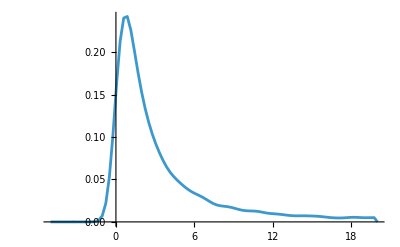

```mathematica
SmoothHistogram[generatedRTData,PlotRange->{{-5,20},All}]
```